## Recurrence relations for SPT kernels (Carlson et al., 0905.0479)

Definitions for generic momenta q_1,...,q_n:

```mathematica
ClearAll[qs,qSel,qSum];
qs[n_]:=Table[q[m],{m,1,n}];
qSel[arr_,n1_,n2_]:=Take[arr,{n1,n2}]
qSum[arr_,n1_,n2_]:=Sum[arr⟦nn⟧,{nn,n1,n2}]
```

The kernels: KerN[n,...]⟦1⟧=F_n(...), KerN[n,...]⟦2⟧=G_n(...).

```mathematica
ClearAll[KerN];
KerN[n_,arr_]:=Module[{k,k1,k2},
k=(qSum[arr,1,n]);
k1[m_]:=(qSum[arr,1,m]);
k2[m_]:=(qSum[arr,m+1,n]);
{
Sum[(KerN[m,qSel[arr,1,m]]⟦2⟧)/((2n+3)(n-1))((1+2n)(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]]⟦1⟧+((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]]⟦2⟧),{m,1,n-1}],
Sum[(KerN[m,qSel[arr,1,m]]⟦2⟧)/((2n+3)(n-1))(3(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]]⟦1⟧+n((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]]⟦2⟧),{m,1,n-1}]
}
];
KerN[1,a_]={1,1};
```

```mathematica
KerNSym[n_,arr_]:=Total[((KerN[n,#1]&)/@Permutations[arr])/(n!)]
```

```mathematica
F2[arr_]:=KerNSym[2,arr]⟦1⟧;
F3[arr_]:=KerNSym[3,arr]⟦1⟧;
G2[arr_]:=KerNSym[2,arr]⟦2⟧;
G3[arr_]:=KerNSym[3,arr]⟦2⟧;
```

## 1-Loop integral

### (c̃)_i parameters and (ĉ)_i kernels (see Appendix A)

```mathematica
biasA={"(b^A)_(δ, 1)","(b^A)_(δ, 2)","(b^A)_(δ, 3)","(b^A)_(δ^2)","(b^A)_c_s"};
biasB={"(b^B)_(δ, 1)","(b^B)_(δ, 2)","(b^B)_(δ, 3)","(b^B)_(δ^2)","(b^B)_c_s"};
```

```mathematica
adelta={"((c̃)^A)_(δ, 1)","((c̃)^A)_(δ, 2 (2))","((c̃)^A)_(δ, 2 (3))","((c̃)^A)_(δ, 3)","((c̃)^A)_(δ, 3 SubscriptBox[c, s])",
"((c̃)^A)_(δ^2)","((c̃)^A)_(δ^2)","((c̃)^A)_(δ^2)","((c̃)^A)_(s^2)","((c̃)^A)_(δ^3)"};
a0={"(c^A)_(δ, 1)","(c^A)_(δ, 2)","(c^A)_(δ, 3)","(c^A)_(δ, 3 SubscriptBox[c, s])","(c^A)_(δ^2)",
"(c^A)_(δ^2)","(c^A)_(δ^3)","(c^A)_(s^2)","(c^A)_(s^2)","(c^A)_(s^3)",
"(c^A)_(st, 1)","(c^A)_(ψ, 1)","(c^A)_(δs^2)"};
```

```mathematica
btheta={"((c̃)^B)_(δ, 1)","((c̃)^B)_(δ, 2 (2))","((c̃)^B)_(δ, 2 (3))","((c̃)^B)_(δ, 3)","((c̃)^B)_(δ, 3 SubscriptBox[c, s])",
"((c̃)^B)_(δ^2)","((c̃)^B)_(δ^2)","((c̃)^B)_(δ^2)","((c̃)^B)_(s^2)","((c̃)^B)_(δ^3)"};
b0={"(c^B)_(δ, 1)","(c^B)_(δ, 2)","(c^B)_(δ, 3)","(c^B)_(δ, 3 SubscriptBox[c, s])","(c^B)_(δ^2)",
"(c^B)_(δ^2)","(c^B)_(δ^3)","(c^B)_(s^2)","(c^B)_(s^2)","(c^B)_(s^3)",
"(c^B)_(st, 1)","(c^B)_(ψ, 1)","(c^B)_(δs^2)"};
```

```mathematica
d1={"((ĉ)^(1))_(δ, 1)"};
d2={"((ĉ)^(2))_(δ, 1)","((ĉ)^(2))_(δ, 2)","((ĉ)^(2))_(δ^2)","((ĉ)^(2))_(s^2)"};
d3={"((ĉ)^(3))_(δ, 1)","((ĉ)^(3))_(δ, 2)","((ĉ)^(3))_(δ, 3)","((ĉ)^(3))_(δ^2)","((ĉ)^(3))_(δ^2)","((ĉ)^(3))_(δ^3)","((ĉ)^(3))_(s^2)","((ĉ)^(3))_(s^2)","((ĉ)^(3))_(s^3)","((ĉ)^(3))_st","((ĉ)^(3))_ψ","((ĉ)^(3))_(δs^2)"};
```

Definitions of parameters in basis of descendents

```mathematica
Clear[asub];
asub[a_,a0_]:={a⟦1⟧->a0⟦1⟧,a⟦2⟧->a0⟦2⟧+7/2 a0⟦8⟧,a⟦3⟧->a0⟦2⟧+7/2 a0⟦8⟧,a⟦4⟧->a0⟦3⟧+45/4 a0⟦10⟧+9/2 a0⟦11⟧+2a0⟦12⟧,a⟦5⟧->a0⟦4⟧,a⟦6⟧->a0⟦5⟧-17/6 a0⟦8⟧,a⟦7⟧->a0⟦5⟧-17/6 a0⟦8⟧ , a⟦8⟧->a0⟦6⟧-137/16 a0⟦10⟧-71/24 a0⟦11⟧-55/42 a0⟦12⟧+7/4 a0⟦13⟧, a⟦9⟧->a0⟦9⟧-3/4 a0⟦10⟧-1/2 a0⟦11⟧-2/7 a0⟦12⟧, a⟦10⟧->a0⟦7⟧+511/72 a0⟦10⟧+25/12 a0⟦11⟧+a0⟦12⟧-17/6 a0⟦13⟧};
```

```mathematica
asub[adelta,a0]
```

{((c̃)^A)_(δ, 1)→(c^A)_(δ, 1),((c̃)^A)_(δ, 2 (2))→(7 (c^A)_(s^2))/2+(c^A)_(δ, 2),((c̃)^A)_(δ, 2 (3))→(7 (c^A)_(s^2))/2+(c^A)_(δ, 2),((c̃)^A)_(δ, 3)→(9 (c^A)_(st, 1))/2+(45 (c^A)_(s^3))/4+(c^A)_(δ, 3)+2 (c^A)_(ψ, 1),((c̃)^A)_(δ, 3 SubscriptBox[c, s])→(c^A)_(δ, 3 SubscriptBox[c, s]),((c̃)^A)_(δ^2)→-(17 (c^A)_(s^2))/6+(c^A)_(δ^2),((c̃)^A)_(δ^2)→-(17 (c^A)_(s^2))/6+(c^A)_(δ^2),((c̃)^A)_(δ^2)→-(71 (c^A)_(st, 1))/24-(137 (c^A)_(s^3))/16+(c^A)_(δ^2)+(7 (c^A)_(δs^2))/4-(55 (c^A)_(ψ, 1))/42,((c̃)^A)_(s^2)→-((c^A)_(st, 1))/2+(c^A)_(s^2)-(3 (c^A)_(s^3))/4-(2 (c^A)_(ψ, 1))/7,((c̃)^A)_(δ^3)→(25 (c^A)_(st, 1))/12+(511 (c^A)_(s^3))/72+(c^A)_(δ^3)-(17 (c^A)_(δs^2))/6+(c^A)_(ψ, 1)}

```mathematica
b0ThetaValues=asub[btheta,b0]/.Join[Thread[b0⟦1;;3⟧->1],{b0⟦12⟧->1},Thread[b0⟦5;;6⟧->-4/21],{b0⟦7⟧->0},Thread[b0⟦8;;9⟧->2/7],Thread[b0⟦10;;11⟧->0],{b0⟦13⟧->0}]
```

{((c̃)^B)_(δ, 1)→1,((c̃)^B)_(δ, 2 (2))→2,((c̃)^B)_(δ, 2 (3))→2,((c̃)^B)_(δ, 3)→3,((c̃)^B)_(δ, 3 SubscriptBox[c, s])→(c^B)_(δ, 3 SubscriptBox[c, s]),((c̃)^B)_(δ^2)→-1,((c̃)^B)_(δ^2)→-1,((c̃)^B)_(δ^2)→-3/2,((c̃)^B)_(s^2)→0,((c̃)^B)_(δ^3)→1}

expressions for ĉ kernels

```mathematica
c1=Array[f,1];
c2=Array[f,4];
c3=Array[f,12];
```

```mathematica
c1⟦1⟧[q1_]:=1;

c2⟦1⟧[q1_,q2_]:=(q1.q2)/(q1.q1);
c2⟦2⟧[q1_,q2_]:=F2[{q1,q2}]-(q1.q2)/(q1.q1);
c2⟦3⟧[q1_,q2_]:=1;
c2⟦4⟧[q1_,q2_]:=(q1.q2)^2/((q1.q1)(q2.q2))-1/3;

c3⟦1⟧[q1_,q2_,q3_]:=1/2((q1.q2+q1.q3)/((q2+q3).(q2+q3))G2[{q2,q3}]+((q1.q2)(q1.q3+q2.q3))/((q2.q2)(q3.q3)));
c3⟦2⟧[q1_,q2_,q3_]:=(q1.q3+q2.q3)/((q2.q2)(q3.q3))(F2[{q1,q2}](q2.q2)-q1.q2);
c3⟦3⟧[q1_,q2_,q3_]:=F3[{q1,q2,q3}]+((q1+q2).q3)/(2 (q2.q2)(q3.q3))(q1.q2-2 F2[{q1,q2}](q2.q2))-(q1.(q2+q3))/(2(q2+q3).(q2+q3))G2[{q2,q3}];
c3⟦4⟧[q1_,q2_,q3_]:=2 (q2.q3)/(q3.q3);
c3⟦5⟧[q1_,q2_,q3_]:=2F2[{q1,q2}]-2(q2.q3)/(q3.q3);
c3⟦6⟧[q1_,q2_,q3_]:=1;
c3⟦7⟧[q1_,q2_,q3_]:=2 (q2.q3)/(q3.q3)((q1.q2)^2/((q1.q1)(q2.q2))-1/3);
c3⟦8⟧[q1_,q2_,q3_]:=2F2[{q1,q2}](((q1+q2).q3)^2/((q1+q2).(q1+q2)(q3.q3))-1/3)-2(q2.q3)/(q3.q3)((q1.q2)^2/((q1.q1)(q2.q2))-1/3);
c3⟦9⟧[q1_,q2_,q3_]:=1/(9(q1.q1)(q2.q2)(q3.q3))(9(q1.q2)(q2.q3)(q1.q3)-3(q1.q3)^2(q2.q2)-3(q1.q2)^2(q3.q3)+(q1.q1)(-3(q2.q3)^2+2(q2.q2)(q3.q3)));
c3⟦10⟧[q1_,q2_,q3_]:=(G2[{q1,q2}]-F2[{q1,q2}])(((q1+q2).q3)^2/((q1+q2).(q1+q2)(q3.q3))-1/3);
c3⟦11⟧[q1_,q2_,q3_]:=G3[{q1,q2,q3}]-F3[{q1,q2,q3}]+2F2[{q1,q2}](F2[{q1+q2,q3}]-G2[{q1+q2,q3}]);
c3⟦12⟧[q1_,q2_,q3_]:=(q1.q2)^2/((q1.q1)(q2.q2))-1/3;
```

### halo kernels in redshift space (see Appendices B and C)

Vector substitutions for k⃗,q⃗ , and ẑ

```mathematica
kqsub={k-> kk{0,0,1},
q-> {qq √(1-x^2) α,qq √(1-x^2) √(1-α^2),qq x}}//Simplify;
zhat = {√(1-μ^2),0,μ};
```

Define symmetrization of a function over two and three variables

```mathematica
q2sym[f_,q1_,q2_]:=Total[(f[#1⟦1⟧,#1⟦2⟧]&)/@Permutations[{q1,q2}]]/Length[Permutations[{q1,q2}]];
q3sym[f_,q1_,q2_,q3_]:=Total[(f[#1⟦1⟧,#1⟦2⟧,#1⟦3⟧]&)/@Permutations[{q1,q2,q3}]]/Length[Permutations[{q1,q2,q3}]];
```

```mathematica
Clear[k,q,aa,bb]
```

```mathematica
subs3[func_,kk_,qq_,x_]:=((q3sym[func,q1,q2,q3]/.{q2+q3->ϵ}/.{q1->k,q2->-q,q3->q}/.{ϵ.ϵ->ϵ0^2}/.{k+ϵ->k}//.{Dot[aa_,-bb_]->-Dot[aa,bb],Dot[-aa_,bb_]->-Dot[aa,bb]}//Simplify)//.{Dot[aa_,ϵ]->0,Dot[ϵ,aa_]->0,ϵ0->0}/.kqsub//Simplify)
```

```mathematica
finduv3[func_,num_]:=Integrate[Series[subs3[func⟦num⟧,kk,qq,x],{qq,∞,0}]//Normal,{x,-1,1}]//Simplify
testuv3[func_,num_]:=Series[subs3[func⟦num⟧,kk,qq,x],{qq,∞,2}];
testuv3alpha[func_,num_]:=subs3[func⟦num⟧,kk,qq,x];
```

```mathematica
c3uv=finduv3[c3,#]&/@Table[i,{i,1,Length[c3]}];
```

```mathematica
Clear[c3ir,c2ir]
```

```mathematica
c3ir[kk_,qq_,x_]=Table[subs3[c3⟦i⟧,kk,qq,x]-1/2 c3uv⟦i⟧,{i,1,Length[c3]}]//Simplify
```

{13/63+(-7 kk^6 x^2+28 kk^4 qq^2 x^2 (-1+x^2)-2 qq^6 (3+4 x^2)+kk^2 qq^4 (-6-17 x^2+44 x^4))/(42 qq^2 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),-4/63 (-1+3 x^2),-(4 (2 qq^4 (1-3 x^2)+kk^4 (3-8 x^2+x^4)+kk^2 qq^2 (5-22 x^2+25 x^4)))/(63 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),0,8/63 (-1+3 x^2),0,2/9-(2 x^2)/3,-(2 (29 qq^4 (1-3 x^2)+kk^4 (119-267 x^2+90 x^4)+2 kk^2 qq^2 (74-235 x^2+219 x^4)))/(189 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),1/9 (-1+3 x^2),4/189 (4+(3 (-1+x^2) (2 qq^4+kk^2 qq^2 (1-5 x^2)+kk^4 (-1+3 x^2)))/((kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x))),(64 kk^2 (kk^2+qq^2) (-1+x^2)^2)/(441 (kk^2+qq^2-2 kk qq x) (kk^2+qq^2+2 kk qq x)),2/9 (-1+3 x^2)}

```mathematica
c2ir[kk_,qq_,x_]=Table[(q2sym[c2⟦i⟧,q1,q2]/.{q1->k-q,q2->q}/.kqsub//Simplify),{i,1,Length[c2]}]//Simplify;

c2irneg[kk_,qq_,x_]=Table[(q2sym[c2⟦i⟧,q1,q2]/.{q1->k+q,q2->-q}/.kqsub//Simplify),{i,1,Length[c2]}]//Simplify;
```

```mathematica
ker1[aa_]:=aa⟦1⟧;
```

Halo Kernels - The aa will be adelta

```mathematica
K2[q1_,q2_,aa_]:=aa⟦1⟧ c2⟦1⟧[q1,q2]+aa⟦2⟧ c2⟦2⟧[q1,q2]+aa⟦6⟧ c2⟦3⟧[q1,q2];
K3[q1_,q2_,q3_,aa_]:=aa⟦1⟧ c3⟦1⟧[q1,q2,q3]+aa⟦3⟧ c3⟦2⟧[q1,q2,q3]+aa⟦4⟧ c3⟦3⟧[q1,q2,q3]+aa⟦7⟧ c3⟦4⟧[q1,q2,q3]+aa⟦8⟧ c3⟦5⟧[q1,q2,q3]+aa⟦10⟧ c3⟦6⟧[q1,q2,q3]+aa⟦9⟧ c3⟦8⟧[q1,q2,q3] ;
```

UV-subtracted Halo Kernels - The aa will be adelta

```mathematica
K2IR[kk_,qq_,x_,aa_]:=aa⟦1⟧ c2ir[kk,qq,x]⟦1⟧+aa⟦2⟧ c2ir[kk,qq,x]⟦2⟧+aa⟦6⟧ c2ir[kk,qq,x]⟦3⟧;
K3IR[kk_,qq_,x_,aa_]:=aa⟦1⟧ c3ir[kk,qq,x]⟦1⟧+aa⟦3⟧ c3ir[kk,qq,x]⟦2⟧+aa⟦4⟧ c3ir[kk,qq,x]⟦3⟧+aa⟦7⟧ c3ir[kk,qq,x]⟦4⟧+aa⟦8⟧ c3ir[kk,qq,x]⟦5⟧+aa⟦10⟧ c3ir[kk,qq,x]⟦6⟧+aa⟦9⟧ c3ir[kk,qq,x]⟦8⟧
```

Second-order redshift-space halo kernels

```mathematica
K2rIR[kk_,qq_,x_,μ_]:=K2IR[kk,qq,x,adelta]+f1 μ^2 K2IR[kk,qq,x,btheta]+μ f1 kk 1/2((q1.zhat)/(q1.q1)+(q2.zhat)/(q2.q2))ker1[btheta] ker1[adelta]+1/2 μ^2 f1^2 kk^2 ((q1.zhat)(q2.zhat))/((q1.q1)(q2.q2))ker1[btheta]ker1[btheta]/.{q1->k-q,q2->q}/.kqsub;
```

Additional third-order kernels for halos in redshift space

```mathematica
keruv={0,0,0,0,0};
```

```mathematica
ker1[q1_,q2_,q3_]:=kk^2(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)ker1[btheta]ker1[btheta]ker1[adelta]; 
ker1sym[kk_,qq_,x_]=q3sym[ker1,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv⟦1⟧=Series[ker1sym[kk,qq,x],{qq,∞,0}]//Normal;
```

```mathematica
ker2[q1_,q2_,q3_]=kk^3(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)ker1[btheta]ker1[btheta]ker1[btheta];
ker2sym[kk_,qq_,x_]=q3sym[ker2,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv⟦2⟧=Series[ker2sym[kk,qq,x],{qq,∞,0}]//Normal;
```

```mathematica
ker3[q1_,q2_,q3_]=kk(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))K2[q1,q2,btheta]ker1[adelta];
ker3sym[kk_,qq_,x_]=q3sym[ker3,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv⟦3⟧=Integrate[Series[ker3sym[kk,qq,x],{qq,∞,0}]//Normal,{x,-1,1}];
```

```mathematica
ker4[q1_,q2_,q3_]=kk^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)K2[q1,q2,btheta]ker1[btheta] ;
ker4sym[kk_,qq_,x_]=q3sym[ker4,q1,q2,q3]/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;keruv⟦4⟧=Series[ker4sym[kk,qq,x],{qq,∞,0}]//Normal;
```

```mathematica
ker5[q1_,q2_,q3_]=kk(q3.zhat)/(q3.q3)K2[q1,q2,adelta]ker1[btheta];
ker5sym[kk_,qq_,x_]=q3sym[ker5,q1,q2,q3]/.{(q2+q3).aa_->0}/.{q1->k,q2->-q,q3->q}/.kqsub//Simplify;
keruv⟦5⟧=Integrate[Series[ker5sym[kk,qq,x],{qq,∞,0}]//Normal,{x,-1,1}]//Simplify;
```

Third-order redshift-space halo kernel

```mathematica
K3r[kk_,qq_,x_,μ_]:=K3IR[kk,qq,x,adelta]+f1 μ^2 K3IR[kk,qq,x,btheta]+f1^2/2 μ^2 (ker1sym[kk,qq,x]-1/2 keruv⟦1⟧)+f1^3/6 μ^3(ker2sym[kk,qq,x]-1/2 keruv⟦2⟧)+f1 μ ( ker3sym[kk,qq,x]-1/2 keruv⟦3⟧)+f1^2 μ^2(ker4sym[kk,qq,x]-1/2 keruv⟦4⟧)+f1 μ ( ker5sym[kk,qq,x]-1/2 keruv⟦5⟧);

K3rIR[kk_,qq_,x_,μ_]=K3r[kk,qq,x,μ]-1/2 Integrate[Series[K3r[kk,qq,x,μ],{qq,∞,2}]//Normal,{x,-1,1}];
```

### 1-Loop integrands

define bias parameters

```mathematica
tb={adelta⟦1⟧->biasA⟦1⟧,adelta⟦6⟧->biasA⟦4⟧,adelta⟦2⟧->biasA⟦2⟧,adelta⟦4⟧->(-15adelta⟦9⟧+biasA⟦3⟧)};
tosym={biasA⟦1⟧->b1,biasA⟦2⟧->b2,biasA⟦3⟧->b3,biasA⟦4⟧->b4,biasA⟦5⟧->b5,Subscript[c, r1]->b6,Subscript[c, r2]->b7,Subscript[c, r3]->b8,Subscript[c, r4]->b9,Subscript[c, r5]->b10,Subscript[c, r6]->b11};
```

P^(22) integrand

```mathematica
PhhRIntegrand22[kk_,qq_,x_,μ_]=Series[Integrate[2 (K2rIR[kk,qq,x,μ])^2/.tb/.b0ThetaValues/.{α->Cos[ϕ]},{ϕ,0,2π}],{μ,0,10}]//Normal//Expand;
```

```mathematica
PhhRIntegrandExp22[kk_,qq_,x_]=Series[PhhRIntegrand22[kk,qq,x,μ],{μ,0,8}]//Normal//Expand;
```

P^(13) integrand

```mathematica
PhhRIntegrand13[kk_,qq_,x_,μ_]=Series[Integrate[6*(adelta[[1]]+f1 μ^2 btheta[[1]])K3rIR[kk,qq,x,μ]/.tb/.b0ThetaValues/.{α->Cos[ϕ]},{ϕ,0,2π}],{μ,0,10}]//Normal//Expand;
```

```mathematica
PhhRIntegrandExp13[kk_,qq_,x_]=Series[PhhRIntegrand13[kk,qq,x,μ],{μ,0,8}]//Normal//Expand;
```

Final Halo integrand

```mathematica
PhhRIntegrandFin13[kk_,qq_,x_]=PhhRIntegrandExp13[kk,qq,x]/.{biasB⟦1⟧->0}//Expand;
PhhRIntegrandFin22[kk_,qq_,x_]=PhhRIntegrandExp22[kk,qq,x]/.{biasB⟦1⟧->0}//Expand;
```

```mathematica
PhhRIntegrandAll13[kk_,qq_,x_,μ_]=PhhRIntegrand13[kk,qq,x,μ]/.{biasB⟦1⟧->0}//Expand;
PhhRIntegrandAll22[kk_,qq_,x_,μ_]=PhhRIntegrand22[kk,qq,x,μ]/.{biasB⟦1⟧->0}//Expand;
```

“Cosmology-free’’ Integrands: removing bias parameters, powers of μ^2 and f from the integrands

```mathematica
μlist={μ^2,μ^4,μ^6,μ^8};
clist1=Outer[Times,μlist,Outer[Times,biasA,biasA]]//Flatten//DeleteDuplicates;
clist2=Outer[Times,biasA,biasA]//Flatten//DeleteDuplicates;
clist3=Outer[Times,biasA,μlist]//Flatten//DeleteDuplicates;
fullclist=Join[clist1,clist2,clist3,μlist];

flist={1,f1,f1^2,f1^3,f1^4};
fullflist=Outer[Times,flist,fullclist]//Flatten;
```

```mathematica
(*P13: Factorizing out bias parameters and powers of μ*)
Clear[coef1,coef2,coef3,coefμ,Kernel,Kf0, Kf1, Kf2, Kf3, Kf4, Kfs]
coef1[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x],clist1];
coef2[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x]/.Thread[clist1->0],clist2];
coef3[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x]/.Thread[clist1->0]/.Thread[clist2->0],clist3];
coefμ[kk_,qq_,x_]=Coefficient[PhhRIntegrandFin13[kk,qq,x]/.Thread[biasA->0],μlist];
Kernel[kk_,qq_,x_]=Join[coef1[kk,qq,x],coef2[kk,qq,x],coef3[kk,qq,x],coefμ[kk,qq,x]];

(*Check that all coefficients are included in Kernel*)
Residual[x_]=PhhRIntegrandFin13[kk,qq,x]-Kernel[kk,qq,x].fullclist/.tb/.tosym//Expand//Simplify
Integrate[Residual[x],{x,-1,1}]
```

-8/63 (151 ((c̃)^A)_(s^2)+6 (-2 ((c̃)^A)_(δ^2)+((c̃)^A)_(δ, 2 (3)))) b1 π (-1+3 x^2)

0

```mathematica
(*Factorizing out powers of f*)
Kf1[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1];
Kf2[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^2];
Kf3[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^3];
Kf4[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^4];
Kf0[kk_,qq_,x_] =Kernel[kk,qq,x]//.f1-> 0;
Kfs[kk_,qq_,x_]=Join[Kf0[kk,qq,x],Kf1[kk,qq,x],Kf2[kk,qq,x],Kf3[kk,qq,x],Kf4[kk,qq,x]];

(*Check that all coefficients are included in Kf's*)
Residual[x_]=PhhRIntegrandFin13[kk,qq,x]-Kfs[kk,qq,x].fullflist/.tb/.tosym;
Integrate[Residual[x],{x,-1,1}]
```

0

```mathematica
(*Sort and take out zeros*)
K13all =Kfs[k,q,x]//Simplify;
N13 = Length[K13all];
Kernel13 = {};
Coef13 = {};
For[i=1,i<=N13,i++, If[K13all[[i]]===0 ,,AppendTo[Kernel13, K13all[[i]]]  && AppendTo[Coef13, fullflist⟦i⟧]]];
Coef13/.tosym
```

{b1^2,b1 b3,b1^2 f1 μ^2,b1 f1 μ^2,b3 f1 μ^2,f1 μ^2,b1^2 f1^2 μ^2,b1^2 f1^2 μ^4,b1 f1^2 μ^2,b1 f1^2 μ^4,f1^2 μ^4,b1 f1^3 μ^4,b1 f1^3 μ^6,f1^3 μ^4,f1^3 μ^6,f1^4 μ^6,f1^4 μ^8}

```mathematica
(*P22: Factorizing out bias parameters and powers of μ*)
Clear[coef1,coef2,coef3,coefμ,Kernel,Kf0, Kf1, Kf2, Kf3, Kf4, Kfs]
coef1[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x],clist1];
coef2[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x]/.Thread[clist1->0],clist2];
coef3[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x]/.Thread[clist1->0]/.Thread[clist2->0],clist3];
coefμ[kk_,qq_,x_,μ_]=Coefficient[PhhRIntegrandFin22[kk,qq,x]/.Thread[biasA->0],μlist];
Kernel[kk_,qq_,x_]=Join[coef1[kk,qq,x,μ],coef2[kk,qq,x,μ],coef3[kk,qq,x,μ],coefμ[kk,qq,x,μ]];

(*Check that all coefficients are included in Kernel*)
PhhRIntegrandFin22[kk,qq,x]-Kernel[kk,qq,x].fullclist/.tb/.tosym//Expand//Simplify
```

0

```mathematica
(*Factorizing out powers of f*)
Kf1[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1];
Kf2[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^2];
Kf3[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^3];
Kf4[kk_,qq_,x_] = Coefficient[Kernel[kk,qq,x],f1^4];
Kf0[kk_,qq_,x_] =Kernel[kk,qq,x]//.f1-> 0;
Kfs[kk_,qq_,x_]=Join[Kf0[kk,qq,x],Kf1[kk,qq,x],Kf2[kk,qq,x],Kf3[kk,qq,x],Kf4[kk,qq,x]];

(*Check that all coefficients are included in Kf's*)
PhhRIntegrandFin22[kk,qq,x]-Kfs[kk,qq,x].fullflist/.tb/.tosym//Expand//Simplify
```

0

```mathematica
(*Sort and take out zeros*)
K22all =Kfs[k,q,x]//Simplify;
N22 = Length[K22all];
Kernel22 = {};
Coef22 = {};
For[i=1,i<=N22,i++, If[K22all[[i]]===0,,AppendTo[Kernel22, K22all[[i]]]  && AppendTo[Coef22, fullflist[[i]]]]];
Coef22/.tosym
Length[Coef22]
```

{b1^2,b1 b2,b1 b4,b2^2,b2 b4,b4^2,b1^2 f1 μ^2,b1 b2 f1 μ^2,b1 b4 f1 μ^2,b1 f1 μ^2,b2 f1 μ^2,b4 f1 μ^2,b1^2 f1^2 μ^2,b1^2 f1^2 μ^4,b1 f1^2 μ^2,b1 f1^2 μ^4,b2 f1^2 μ^2,b2 f1^2 μ^4,b4 f1^2 μ^2,b4 f1^2 μ^4,f1^2 μ^4,b1 f1^3 μ^4,b1 f1^3 μ^6,f1^3 μ^4,f1^3 μ^6,f1^4 μ^4,f1^4 μ^6,f1^4 μ^8}

28

At the end of the day, you get the cosmology - free Kernel13 and Kernel22 with Coef13 and Coef22, respectively.

### 1-loop integrals by Dim. Reg.

Auxiliary function

```mathematica
J2[k_,ν1_,ν2_]:=1/(2π)^3(Gamma[3/2-ν1]Gamma[3/2-ν2]Gamma[ν1+ν2-3/2])/(Gamma[ν1]Gamma[ν2]Gamma[3-ν1-ν2])π^(3/2)k^(3-2ν1-2ν2);
```

```mathematica
FortranForm[(1/(2π)^3(Gamma[3/2-ν1]Gamma[3/2-ν2]Gamma[ν1+ν2-3/2])/(Gamma[ν1]Gamma[ν2]Gamma[3-ν1-ν2])π^(3/2)//Simplify)//.{ν1-> n1, ν2-> n2} ]/.{Gamma-> gamma}
```

(gamma(1.5 - n1)*gamma(1.5 - n2)*gamma(-1.5 + n1 + n2))/
     -  (8.*Pi**1.5*gamma(n1)*gamma(3 - n1 - n2)*gamma(n2))

Dim. Reg.

13 Diagram

```mathematica
Clear[P13];
P13 = {} ;
Do[
Clear[Tab13,Integrand13];
Integrand13 =( Apart[Kernel13⟦j⟧]/.{k^2+q^2-2 k q x-> kmq^2}/.{-k^2-q^2+2 k q x->- kmq^2}/.{k^2+q^2+2 k q x-> kmq^2}/.{x-> (kmq^2-k^2-q^2)/(2k q)})//Expand ;
(*The following gives ν1, ν2 and the coefficient for the different terms*)
Tab13 = Table[{-1/2 q D[Integrand13⟦i⟧ ,q]/Integrand13⟦i⟧,-1/2 kmq D[Integrand13⟦i⟧ ,kmq]/Integrand13⟦i⟧,Integrand13⟦i⟧/.{q->1,kmq->1,k->1}},{i,1,Length[Integrand13]}] ;
AppendTo[P13,Sum[Tab13⟦i,3⟧J2[1,Tab13⟦i,1⟧+n1,Tab13⟦i,2⟧],{i,1,Length[Tab13]}]//FullSimplify];
,{j,Length[Kernel13]}]
P13
```

{(9 Tan[n1 π])/(56 n1 (-6+11 n1-6 n1^2+n1^3)),-Tan[n1 π]/(7 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(9 Tan[n1 π])/(28 n1 (-6+11 n1-6 n1^2+n1^3)),(3 (-1+3 n1) Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),-Tan[n1 π]/(7 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),0,0,0,-(9 Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(9 (1+2 n1) Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(3 (-5+3 n1) Tan[n1 π])/(56 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),0,0,-(9 Tan[n1 π])/(28 n1 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),(9 Tan[n1 π])/(28 (-6+5 n1+5 n1^2-5 n1^3+n1^4)),0,0}

```mathematica
(* Clear zeros *)
Clear[C13,M13];
 C13={} ; M13 = {} ;
For[i=1,i≤Length[P13],i++, If[P13[[i]]===0,,AppendTo[M13, 1/(2 π)P13⟦i⟧/(Tan[n1 π]/(14 π(-3+n1) (-2+n1) (-1+n1) n1))//Simplify]  && AppendTo[C13, Coef13⟦i⟧/.tosym] ]];
C13
M13
```

{b1^2,b1 b3,b1^2 f1 μ^2,b1 f1 μ^2,b3 f1 μ^2,b1 f1^2 μ^2,b1 f1^2 μ^4,f1^2 μ^4,f1^3 μ^4,f1^3 μ^6}

{9/8,-1/(1+n1),9/4,(3 (-1+3 n1))/(4 (1+n1)),-1/(1+n1),-9/(4+4 n1),(9+18 n1)/(4+4 n1),(3 (-5+3 n1))/(8 (1+n1)),-9/(4+4 n1),(9 n1)/(4+4 n1)}

```mathematica
M13C = Table[FortranForm[M13⟦i⟧],{i,1,Length[M13]}];
Export["M13.txt",M13C, "Table"];
Export["C13.txt",C13/.{μ-> m}, "Table"];
```

22 Diagram

```mathematica
(*Clear[P22];
P22 = {} ;
Do[
Clear[Tab22,Integrand22];
Integrands22 = Kernel22[[j]]/.{x-> -(kmq^2-k^2-q^2)/(2k q)}//Expand;
(*The following gives ν1, ν2 and the coefficient for the different terms*)
Tab22 = Table[{-1/2q D[Integrands22⟦i⟧ ,q]/Integrands22⟦i⟧,-1/2kmq D[Integrands22⟦i⟧ ,kmq]/Integrands22⟦i⟧,Integrands22⟦i⟧/.{q->1,kmq->1,k->1}},{i,1,Length[Integrands22]}];
AppendTo[P22,Sum[Tab22⟦i,3⟧J2[1,Tab22⟦i,1⟧+n1,Tab22⟦i,2⟧+n2]/J2[1,n1,n2],{i,1,Length[Tab22]}]//FullSimplify];
,{j,Length[Kernel22]}];
P12*)
```

```mathematica
(* The above gives P22⟦6⟧ = 4 + π because there is only a 4π factor, and the length is 2 but not one: it should be 4π *)
P22={((6+n1 (1+2 n1) (-7+n1+2 n1^2)-7 n2+2 n1 (-3+n1 (19+n1 (-5+4 (-3+n1) n1))) n2+(-13+2 n1 (19+6 n1-4 n1^2)) n2^2+2 (2+n1 (-5-4 n1+8 n1^2)) n2^3+4 (1-6 n1) n2^4+8 n1 n2^5) π)/(2 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (n1^2 (1-11 n2)+2 n1^3 (5+7 n2)+(-3+2 n2) (6+n2 (8+5 n2))+n1 (-12+n2 (-38+n2 (-11+14 n2)))) π Gamma[n1] Gamma[n2])/(7 Gamma[2+n1] Gamma[2+n2]),2 ((-3+2 n1)/n2+(-3+2 n2)/n1) π,(4 (48-2 n1 (1+10 n1)-2 n2+3 n1 (17+7 n1) n2+(-20+7 n1 (3+7 n1)) n2^2) π Gamma[n2])/(49 n1 (1+n1) Gamma[2+n2]),(8 (3-2 n2+n1 (-2+7 n2)) π)/(7 n1 n2),4π,((-3+2 n1+2 n2) (-2+3 n2+4 n1^4 n2+(3-2 n2) n2^2+2 n1^3 (-1+n2) (1+2 n2)+n1 (1+2 n2) (3+2 (-2+n2) n2 (1+n2))+n1^2 (3+2 n2 (-5+2 (-1+n2) n2))) π)/(n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (-3+2 n1+2 n2) (2+n2 (4+5 n2)+n1^2 (5+7 n2)+n1 (4+n2 (10+7 n2))) π)/(7 n1 (1+n1) n2 (1+n2)),(2 (n1+n2) (-3+2 n1+2 n2) π)/(n1 n2),((-3+2 n1+2 n2) (28 n1^4 n2+(-2+n2) (5+n2) (-1+2 n2)+n1^3 (2-46 n2+28 n2^2)+n1^2 (5+2 n2 (-19+14 (-1+n2) n2))+n1 (-23+2 n2 (47+n2 (-19+n2 (-23+14 n2))))) π)/(7 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (-3+2 n1+2 n2) (-58+7 n1^2 (5+7 n2)+n2 (4+35 n2)+n1 (4+7 n2 (2+7 n2))) π)/(49 n1 (1+n1) n2 (1+n2)),(2 (-3+2 n1+2 n2) (-8+7 n1+7 n2) π)/(7 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+(-1+n1) n1 (1+2 n1)-n2-2 n1 (1+n1) n2-(1+2 n1) n2^2+2 n2^3) π)/(4 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((1+n1+n2) (2+n1+n2) π Gamma[n1] Gamma[n2] Gamma[1/2+n1+n2])/(Gamma[2+n1] Gamma[2+n2] Gamma[-3/2+n1+n2]),((-3+2 n1+2 n2) (6+n1-2 n1^2+n2-2 n2^2) π)/(4 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (38+112 n1^3 n2+(41-66 n2) n2+2 n1^2 (-33+2 n2 (-9+28 n2))+n1 (41+4 n2 (-58+n2 (-9+28 n2)))) π)/(28 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),-((-3+2 n1+2 n2) (9+3 n1+3 n2+7 n1 n2) π Gamma[n2])/(7 n1 (1+n1) Gamma[2+n2]),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (5+5 n1+5 n2+7 n1 n2) π Gamma[n2])/(7 n1 (1+n1) Gamma[2+n2]),((3-2 n1-2 n2) π)/(n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) π)/(n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (50+98 n1^3 n2-n2 (9+35 n2)+7 n1^2 (-5+2 n2 (-9+14 n2))+n1 (-9+2 n2 (-33+7 n2 (-9+7 n2)))) π)/(98 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+n1+4 n1^3+n2-8 n1^2 n2+4 n2^3-8 n1 n2 (1+n2)) π)/(4 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(2 (2+n1+n2) π Gamma[n1] Gamma[n2] Gamma[3/2+n1+n2])/(Gamma[2+n1] Gamma[2+n2] Gamma[-3/2+n1+n2]),-((-3+2 n1+2 n2) (-1+2 n1+2 n2) (-2+7 n1+7 n2) π)/(28 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (26+56 n1^3 n2+(9-38 n2) n2+2 n1^2 (-19+2 n2 (-9+28 n2))+n1 (9+4 n2 (-21+n2 (-9+14 n2)))) π)/(28 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(3 (-3+2 n1+2 n2) (-1+2 n1+2 n2) π)/(16 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (1+2 (n1^2-4 n1 n2+n2^2)) π)/(8 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (3+2 n1+2 n2) π)/(16 n1 (1+n1) n2 (1+n2))};
```

```mathematica
(* Clear zeros *)
Clear[C22,M22]; C22={} ; M22 = {} ;
For[i=1,i≤Length[P22],i++, If[P22[[i]]===0,,AppendTo[M22, P22⟦i⟧/(2π)//FunctionExpand//Simplify]  && AppendTo[C22, Coef22⟦i⟧/.tosym] ]];
C22
```

{b1^2,b1 b2,b1 b4,b2^2,b2 b4,b4^2,b1^2 f1 μ^2,b1 b2 f1 μ^2,b1 b4 f1 μ^2,b1 f1 μ^2,b2 f1 μ^2,b4 f1 μ^2,b1^2 f1^2 μ^2,b1^2 f1^2 μ^4,b1 f1^2 μ^2,b1 f1^2 μ^4,b2 f1^2 μ^2,b2 f1^2 μ^4,b4 f1^2 μ^2,b4 f1^2 μ^4,f1^2 μ^4,b1 f1^3 μ^4,b1 f1^3 μ^6,f1^3 μ^4,f1^3 μ^6,f1^4 μ^4,f1^4 μ^6,f1^4 μ^8}

```mathematica
M22Verif={(6+n1^4 (4-24 n2)-7 n2+8 n1^5 n2-13 n2^2+4 n2^3+4 n2^4+n1^2 (-13+38 n2+12 n2^2-8 n2^3)+2 n1^3 (2-5 n2-4 n2^2+8 n2^3)+n1 (-7-6 n2+38 n2^2-10 n2^3-24 n2^4+8 n2^5))/(4 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(-18+n1^2 (1-11 n2)-12 n2+n2^2+10 n2^3+2 n1^3 (5+7 n2)+n1 (-12-38 n2-11 n2^2+14 n2^3))/(7 n1 (1+n1) n2 (1+n2)),(-3 n1+2 n1^2+n2 (-3+2 n2))/(n1 n2),(-4 (-24+n2+10 n2^2)+2 n1 (-2+51 n2+21 n2^2)+n1^2 (-40+42 n2+98 n2^2))/(49 n1 (1+n1) n2 (1+n2)),(4 (3-2 n2+n1 (-2+7 n2)))/(7 n1 n2),2,((-3+2 n1+2 n2) (-2+3 n2+4 n1^4 n2+3 n2^2-2 n2^3+n1^3 (-2-2 n2+4 n2^2)+n1^2 (3-10 n2-4 n2^2+4 n2^3)+n1 (3+2 n2-10 n2^2-2 n2^3+4 n2^4)))/(2 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (2+4 n2+5 n2^2+n1^2 (5+7 n2)+n1 (4+10 n2+7 n2^2)))/(7 n1 (1+n1) n2 (1+n2)),((n1+n2) (-3+2 n1+2 n2))/(n1 n2),((-3+2 n1+2 n2) (10-23 n2+28 n1^4 n2+5 n2^2+2 n2^3+n1^3 (2-46 n2+28 n2^2)+n1^2 (5-38 n2-28 n2^2+28 n2^3)+n1 (-23+94 n2-38 n2^2-46 n2^3+28 n2^4)))/(14 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-58+4 n2+35 n2^2+7 n1^2 (5+7 n2)+n1 (4+14 n2+49 n2^2)))/(49 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-8+7 n1+7 n2))/(7 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+2 n1^3-n2-n2^2+2 n2^3-n1^2 (1+2 n2)-n1 (1+2 n2+2 n2^2)))/(8 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((1+n1+n2) (2+n1+n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2))/(8 n1 (1+n1) n2 (1+n2)),-((-3+2 n1+2 n2) (-6-n1+2 n1^2-n2+2 n2^2))/(8 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (38+41 n2+112 n1^3 n2-66 n2^2+2 n1^2 (-33-18 n2+56 n2^2)+n1 (41-232 n2-36 n2^2+112 n2^3)))/(56 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),-((-3+2 n1+2 n2) (9+3 n1+3 n2+7 n1 n2))/(14 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (5+5 n1+5 n2+7 n1 n2))/(14 n1 (1+n1) n2 (1+n2)),(3-2 n1-2 n2)/(2 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2))/(2 n1 n2),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (50-9 n2+98 n1^3 n2-35 n2^2+7 n1^2 (-5-18 n2+28 n2^2)+n1 (-9-66 n2-126 n2^2+98 n2^3)))/(196 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (2+n1+4 n1^3+n2-8 n1 n2-8 n1^2 n2-8 n1 n2^2+4 n2^3))/(8 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((2+n1+n2) (-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2))/(8 n1 (1+n1) n2 (1+n2)),-((-3+2 n1+2 n2) (-1+2 n1+2 n2) (-2+7 n1+7 n2))/(56 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (26+9 n2+56 n1^3 n2-38 n2^2+2 n1^2 (-19-18 n2+56 n2^2)+n1 (9-84 n2-36 n2^2+56 n2^3)))/(56 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),(3 (-3+2 n1+2 n2) (-1+2 n1+2 n2))/(32 n1 (1+n1) n2 (1+n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (1+2 n1^2-8 n1 n2+2 n2^2))/(16 n1 (1+n1) (-1+2 n1) n2 (1+n2) (-1+2 n2)),((-3+2 n1+2 n2) (-1+2 n1+2 n2) (1+2 n1+2 n2) (3+2 n1+2 n2))/(32 n1 (1+n1) n2 (1+n2))};
M22-M22Verif//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
M22C = Table[FortranForm[M22Verif⟦i⟧],{i,1,Length[M22]}];
Export["M22.txt",M22C, "Table"];
Export["C22.txt",C22/.{μ-> m}, "Table"];
```

## Resummation ‘all terms’ - to put to Taylor order n = 8

### Power spectra imports

```mathematica
(*DS1 cosmology: Ωm = 0.295 , Ωb = 0.0468, ΩΛ = 0.705, h = 0.688, ns = 0.9676, σ8 = 0.835, As = 2.43 10^-9*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
p11DS1 = Interpolation[Import["PlinearDS1_matterpower.dat"], InterpolationOrder->2];
```

```mathematica
ns=0.9676;
```

```mathematica
plindat=Import["PlinearDS1_matterpower.dat"];
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^ns},{i,1,30}];
plindat2=Join[pextra,plindat];
plin=Interpolation[Log[plindat2]];
```

```mathematica
Clear[Plin];
khigh=40.;
pcut[k_]= Exp[plin[Log[k]]](*Exp[-(k/khigh)]*);
Plin[k_]=pcut[k];
```

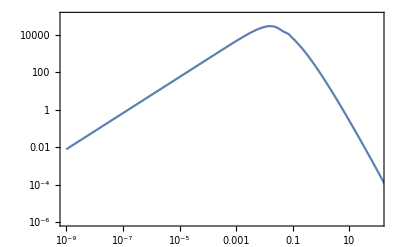

```mathematica
LogLogPlot[Plin[k],{k,10^-9,1000},Frame->True,PlotRange->{{0.000000001,100},{10^-6,10^5}}]
```

### Ξ0 Ξ2 by FFTLog

```mathematica
(* Nmax log k bins, form kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
Λresum =0.12;
CoeffPowIR[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Exp[-kn⟦i⟧^2/Λresum^2]/kn⟦i⟧^2 Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

General::munfl: Exp[-1309.68] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6031.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-27777.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

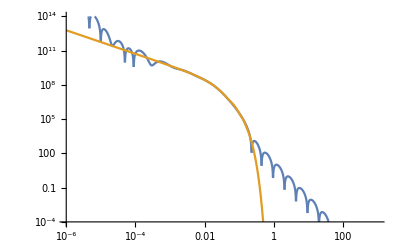

```mathematica
biasA=-2.6//N;
NmaxA=20;
kminA=10^-5;
kmaxA=20;
cnA=CoeffPowIR[biasA,NmaxA,kminA,kmaxA];
kn=kBins[NmaxA,kminA,kmaxA];
Pdq2[k_] = Re[ Total[cnA⟦All,1⟧k^cnA⟦All,2⟧]];
LogLogPlot[{Abs[Pdq2[k]],Exp[-k^2/Λresum^2]/k^2 Plin[k]},{k,.000001,1000},PlotRange->{10^-4,10^14}]
```

```mathematica
Mtilde0=cnA⟦All,1⟧ * (-1/(2 π^2))Gamma[2 + cnA⟦All,2⟧] Sin[(cnA⟦All,2⟧ π)/2];
Mtilde2=cnA⟦All,1⟧ * (1/(2 π^2))√π 2^(1+cnA⟦All,2⟧)Gamma[(3+2+ cnA⟦All,2⟧)/2]/Gamma[(2-cnA⟦All,2⟧)/2] ;
Ξ0[q_] =Re[ Mtilde0.q^(-cnA⟦All,2⟧-3) ];
Ξ2[q_] =Re[ Mtilde2.q^(-cnA⟦All,2⟧-3) ];
Ξ0[q_] = -Ξ0[q]+Ξ0[0.01];
```

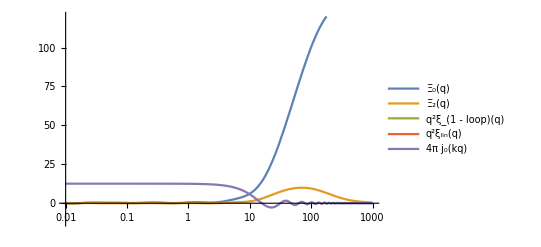

```mathematica
ktest = 0.2 ;
p1=LogLinearPlot[{Ξ0[q] ,Ξ2[q],q^2 ξE1loopFFT[q],q^2 ξ11FFT[q] ,4π SphericalBesselJ[0,ktest q] }, { q , 10^-2, 1000},PlotRange->{-12,120},PlotLegends-> {"Ξ_0(q)", "Ξ_2(q)","q^2ξ_(1 - loop)(q)", "q^2ξ_lin(q)", "4π j_0(kq)" }]
(*Export["IRcorrections.pdf",p1]*)
```

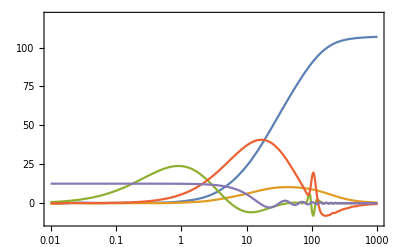

-Graphics-

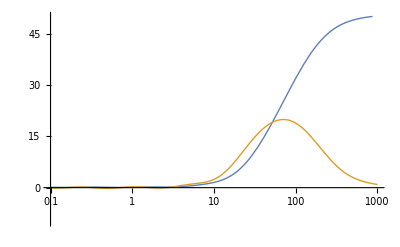

```mathematica
LogLinearPlot[{   2/3(Ξ0[q]-Ξ2[q]),2 Ξ2[q], X1[1][q] ,Y1[1][q]} , { q , 10^-1, 1000},PlotRange->{-10,50},PlotStyle->{Thick, Thick, Dashed ,Dashed}]
```

### IR-correction integrands

For fast computation, I compute only a, b, c up to 4 and l, lpr = 4 (which is enough at the order n_X and n_Y that we work)

```mathematica
SetDirectory[NotebookDirectory[]];
```

compute spherical bessel derivatives j_l^(c)(x)

```mathematica
Clear[jc]
Do[ Monitor[jc[c][l][x_] =  D[SphericalBesselJ[l,x],{x,c}]//Simplify ,{ c , l }], {c, 0,4} , {l , 0,8}]
```

compute n_j^b(l’)

```mathematica
Clear[n];
Do[ n[b][j][lpr] = Integrate[ (2(j + lpr) + 1)/2 μ^b LegendreP[j + lpr , μ ] LegendreP[lpr , μ] , { μ , -1 , 1}], { b, 0,4} , {j , -4,4} , {lpr,0,4,2}]
```

compute (I^a)_(l,l')(k,q)

```mathematica
orderTaylor = 3;
Do[ Monitor[Iint[a][l][lpr][k_,q_] = Integrate[(LegendreP[l,μk] μk^a Normal[ Series[ ⅇ^(-λ k^2/2(2+ff)ff X1 (μk^2-β)) , {λ , 0 , orderTaylor}]]LegendreP[lpr,μk]/.λ->1//FunctionExpand),{μk,-1,1}]//Simplify ,{a, l , lpr}], { a ,0,4}, {l,{0,2,4}} , {lpr,0,8}]
```

compute (L_(l,l'))^abc(k,q)

```mathematica
Clear[L];
Monitor[ Do[ L[a][b][c][l][lpr][k_,q_] = Sum[ (ⅈ)^c(-ⅈ)^j n[b][j][lpr] *jc[c][lpr + j][k q] *Iint[a][l][lpr+j][k,q] , {j , If[ lpr-b<0,-lpr,-b],b}] , {a,0,4},{b,0,4},{c,0,4},{l,0,4,2}, {lpr ,0,4,2}], { a, b,c,l,lpr}] ;
```

compute κ_abc(L_(l,l'))^abc(k,q) (||)_0

```mathematica
fullterm1 = Coefficient[ Series[ Exp[-1/2 λ k^2 Y1( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)] , {λ , 0 , 1}]//Normal , λ^1]//Expand;
fullterm2 = Coefficient[ Series[ Exp[-1/2 λ k^2 Y1 ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)] , {λ , 0 , 2}]//Normal , λ^2]//Expand;
Clear[K1,K2]
K1[l_][lpr_][k_,q_] =  Sum[ Coefficient[ μk μq kdq fullterm1 , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];
K2[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq fullterm2 , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];
```

Q_0 for IR-resummation

```mathematica
Q0[k_,q_,l_,lpr_]=    (2l+1)/2 ⅇ^(-k^2/2(X1+Y1 α))   ⅇ^(-k^2/2(2+ff)ff X1 β)(L[0][0][0][l][lpr][k,q]+K1[l][lpr][k,q] +0K2[l][lpr][k,q] )  ;
```

Q_1 for IR-resummation

```mathematica
yorder =1;
exps = Exp[-1/2 λ1 k^2 Y1 ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)]Exp[ λ2 k^2/2( X1(1 + μk^2 ff(2+ff))  + Y1 ( kdq^2 + 2 μk μq ff kdq + ff^2 μk^2 μq^2))] ;
expand=(Series[ Series[ Series[ exps , { λ1 , 0 , yorder}]//Normal , {λ2, 0 ,1}]//Normal , { Y1 , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1} ;

J[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq expand , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}] ;
Q1[k_,q_,l_,lpr_]= (2l + 1)/2 ⅇ^(-k^2/2( X1 + α Y1)) ⅇ^(-k^2/2(2+ff)ff X1 β)J[l][lpr][k,q] ;
```

```mathematica
SBrep5={SphericalBesselJ[5,x_]->9/x SphericalBesselJ[4,x]-SphericalBesselJ[3,x]};
SBrep3={SphericalBesselJ[3,x_]-> 5/x SphericalBesselJ[2,x]-SphericalBesselJ[1,x] };
SBrep1={SphericalBesselJ[1,x_]-> x/3(SphericalBesselJ[0,x]+SphericalBesselJ[2,x])};
Fakerep={SphericalBesselJ[0,x_ ]-> j0,SphericalBesselJ[2,x_ ]-> j2,  SphericalBesselJ[4,x_ ]-> j4,SphericalBesselJ[6,x_ ]-> j6};
ab={α-> 0,β-> 0};
```

```mathematica
Xp = {k^3 X1,k^5 X1^2,k^7 X1^3,k^9 X1^4};
YXp={k^3 Y1,k^5 Y1 X1,k^7 Y1 X1^2,k^9 Y1 X1^3};
jlist02 = {j0, j2};
jlist024={j0,j2,j4};
jklist = {j0 k,j2 k,j4 k} ;
j2k2YXp={j2  k^3 X1 Y1,j2 k^5 X1^2 Y1,j2 k^7 X1^3 Y1,j2 k^9 X1^4 Y1};
j2k2YXpqm2={q^-2 j2  k^3 X1 Y1,q^-2 j2 k^5 X1^2 Y1,q^-2 j2 k^7 X1^3 Y1,q^-2 j2 k^9 X1^4 Y1};
megalist=Join[jklist,Outer[Times,Xp,  jlist02],Outer[Times,YXp,jlist024],j2k2YXp,{j2 k Y1}]//Flatten
megalistq=Join[jklist,Outer[Times,Xp,  jlist02],Outer[Times,YXp,jlist024],j2k2YXpqm2,{q^-2 j2 k Y1}]//Flatten
Length[megalistq]
```

{j0 k,j2 k,j4 k,j0 k^3 X1,j2 k^3 X1,j0 k^5 X1^2,j2 k^5 X1^2,j0 k^7 X1^3,j2 k^7 X1^3,j0 k^9 X1^4,j2 k^9 X1^4,j0 k^3 Y1,j2 k^3 Y1,j4 k^3 Y1,j0 k^5 X1 Y1,j2 k^5 X1 Y1,j4 k^5 X1 Y1,j0 k^7 X1^2 Y1,j2 k^7 X1^2 Y1,j4 k^7 X1^2 Y1,j0 k^9 X1^3 Y1,j2 k^9 X1^3 Y1,j4 k^9 X1^3 Y1,j2 k^3 X1 Y1,j2 k^5 X1^2 Y1,j2 k^7 X1^3 Y1,j2 k^9 X1^4 Y1,j2 k Y1}

{j0 k,j2 k,j4 k,j0 k^3 X1,j2 k^3 X1,j0 k^5 X1^2,j2 k^5 X1^2,j0 k^7 X1^3,j2 k^7 X1^3,j0 k^9 X1^4,j2 k^9 X1^4,j0 k^3 Y1,j2 k^3 Y1,j4 k^3 Y1,j0 k^5 X1 Y1,j2 k^5 X1 Y1,j4 k^5 X1 Y1,j0 k^7 X1^2 Y1,j2 k^7 X1^2 Y1,j4 k^7 X1^2 Y1,j0 k^9 X1^3 Y1,j2 k^9 X1^3 Y1,j4 k^9 X1^3 Y1,(j2 k^3 X1 Y1)/q^2,(j2 k^5 X1^2 Y1)/q^2,(j2 k^7 X1^3 Y1)/q^2,(j2 k^9 X1^4 Y1)/q^2,(j2 k Y1)/q^2}

28

```mathematica
coefQ1=Table[Coefficient[Series[k Q1[k, q, l,lp]/.SBrep3/.SBrep1/.Fakerep/.ab,{k,0,9}]//Normal,megalist]/.{X1-> 0,Y1-> 0,q-> 1}//Simplify,{l,{0,2}},{lp,{0,2}}] ;
(*Verification*)
Table[(coefQ1⟦l/2+1,lp/2+1⟧.megalistq- Series[k Q1[k, q, l,lp]/.SBrep3/.SBrep1 /.Fakerep/.ab,{k,0,9}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]
coefQ1//MatrixForm
```

{{0,0},{0,0}}

((1
0
0
0
0
1/120 (-15-20 ff-22 ff^2-12 ff^3-3 ff^4)
0
1/840 (35+70 ff+119 ff^2+124 ff^3+81 ff^4+30 ff^5+5 ff^6)
0
(-945-2520 ff-5796 ff^2-8856 ff^3-9854 ff^4-7720 ff^5-3900 ff^6-1120 ff^7-140 ff^8)/120960
0
0
0
0
1/180 (-15-20 ff-22 ff^2-12 ff^3-3 ff^4)
1/630 (105+140 ff+133 ff^2+66 ff^3+12 ff^4)
0
1/840 (35+70 ff+119 ff^2+124 ff^3+81 ff^4+30 ff^5+5 ff^6)
(-105-210 ff-336 ff^2-336 ff^3-205 ff^4-70 ff^5-10 ff^6)/1260
0
(-315-840 ff-1932 ff^2-2952 ff^3-3098 ff^4-2200 ff^5-1020 ff^6-280 ff^7-35 ff^8)/30240
(3465+9240 ff+20559 ff^2+30690 ff^3+31207 ff^4+21380 ff^5+9465 ff^6+2450 ff^7+280 ff^8)/166320
0
0
0
0
0
0) | (0
0
0
0
0
0
-1/210 ff (14+19 ff+12 ff^2+3 ff^3)
0
(ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5))/1260
0
-(ff (1386+4257 ff+7524 ff^2+9071 ff^3+7450 ff^4+3855 ff^5+1120 ff^6+140 ff^7))/166320
0
0
0
(ff (70+123 ff+100 ff^2+28 ff^3))/4200
-(ff (294+357 ff+200 ff^2+44 ff^3))/2940
(ff (490+749 ff+380 ff^2+64 ff^3))/29400
-(ff (70+239 ff+400 ff^2+349 ff^3+160 ff^4+30 ff^5))/12600
(ff (686+1414 ff+1580 ff^2+1017 ff^3+360 ff^4+55 ff^5))/8820
-(ff (5390+12859 ff+14960 ff^2+9939 ff^3+3460 ff^4+480 ff^5))/323400
(ff (2310+15411 ff+42900 ff^2+65446 ff^3+60890 ff^4+34515 ff^5+11060 ff^6+1540 ff^7))/3326400
-(ff (61446+179025 ff+299640 ff^2+320318 ff^3+224650 ff^4+100665 ff^5+26320 ff^6+3080 ff^7))/2328480
(ff (210210+681681 ff+1204060 ff^2+1353846 ff^3+986190 ff^4+453065 ff^5+118860 ff^6+13440 ff^7))/33633600
1/840 ff (182+163 ff+36 ff^2)
-1/840 ff (182+319 ff+272 ff^2+119 ff^3+20 ff^4)
(ff (6006+15675 ff+22484 ff^2+19794 ff^3+10650 ff^4+3235 ff^5+420 ff^6))/73920
-(ff (78078+270699 ff+542256 ff^2+713453 ff^3+639370 ff^4+389085 ff^5+154420 ff^6+36155 ff^7+3780 ff^8))/4324320
0)
(0
0
0
0
0
-1/42 ff (14+19 ff+12 ff^2+3 ff^3)
0
1/252 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
0
-(ff (1386+4257 ff+7524 ff^2+9071 ff^3+7450 ff^4+3855 ff^5+1120 ff^6+140 ff^7))/33264
0
0
0
0
-1/63 ff (14+19 ff+12 ff^2+3 ff^3)
1/126 ff (56+73 ff+42 ff^2+9 ff^3)
0
1/252 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
-(ff (924+2013 ff+2332 ff^2+1550 ff^3+560 ff^4+85 ff^5))/2772
0
-(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/8316
(ff (48048+146289 ff+253110 ff^2+279487 ff^3+201860 ff^4+92775 ff^5+24710 ff^6+2905 ff^7))/432432
0
0
0
0
0
0) | (0
1
0
0
0
0
1/168 (-21-44 ff-58 ff^2-36 ff^3-9 ff^4)
0
(231+726 ff+1551 ff^2+1868 ff^3+1317 ff^4+510 ff^5+85 ff^6)/5544
0
(-27027-113256 ff-334620 ff^2-596232 ff^3-732778 ff^4-610520 ff^5-318660 ff^6-92960 ff^7-11620 ff^8)/3459456
0
0
0
(-35+2 ff+91 ff^2+100 ff^3+32 ff^4)/1680
(-245-462 ff-545 ff^2-300 ff^3-66 ff^4)/1176
(8085+16786 ff+19283 ff^2+10820 ff^3+2176 ff^4)/129360
(1155+1144 ff-2794 ff^2-8380 ff^3-8897 ff^4-4460 ff^5-880 ff^6)/110880
(8085+23716 ff+47168 ff^2+52700 ff^3+34341 ff^4+12240 ff^5+1870 ff^6)/77616
(-105105-328328 ff-654082 ff^2-759980 ff^3-511461 ff^4-185980 ff^5-27840 ff^6)/3363360
(-45045-91806 ff+23595 ff^2+461760 ff^3+952577 ff^4+1006450 ff^5+611385 ff^6+203980 ff^7+29120 ff^8)/17297280
(-315315-1255254 ff-3518229 ff^2-5935800 ff^3-6456811 ff^4-4591670 ff^5-2077815 ff^6-546140 ff^7-63910 ff^8)/12108096
(105105+438438 ff+1237665 ff^2+2167360 ff^3+2454579 ff^4+1816470 ff^5+850475 ff^6+228900 ff^7+26880 ff^8)/13453440
1/336 (273+394 ff+311 ff^2+84 ff^3)
(-3003-7480 ff-11990 ff^2-10276 ff^3-4567 ff^4-820 ff^5)/7392
(39039+138138 ff+334191 ff^2+479648 ff^3+427773 ff^4+234090 ff^5+72325 ff^6+9660 ff^7)/384384
(-117117-537108 ff-1738308 ff^2-3495336 ff^3-4668838 ff^4-4249040 ff^5-2620980 ff^6-1053080 ff^7-249445 ff^8-26460 ff^9)/6918912
0))

```mathematica
Export["Q1.txt",Table[FortranForm[coefQ1⟦2,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
```

```mathematica
coefQ0=Table[Coefficient[Series[k Q0[k, q, l,lp]/.SBrep3/.SBrep1/.Fakerep/.ab,{k,0,9}]//Normal,megalist]/.{X1-> 0,Y1-> 0}/.{q-> 1}//Simplify,{l,{0,2}},{lp,{0,2}}] ;
(*Verification*)
Table[(coefQ0⟦l/2+1,lp/2+1⟧.megalistq- Series[k Q0[k, q, l,lp]/.SBrep3/.SBrep1 /.Fakerep/.ab,{k,0,9}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]
coefQ0//MatrixForm
```

{{0,0},{0,0}}

((1
0
0
1/6 (-3-2 ff-ff^2)
0
1/120 (15+20 ff+22 ff^2+12 ff^3+3 ff^4)
0
(-35-70 ff-119 ff^2-124 ff^3-81 ff^4-30 ff^5-5 ff^6)/1680
0
(105+280 ff+644 ff^2+984 ff^3+846 ff^4+360 ff^5+60 ff^6)/40320
0
1/18 (-3-2 ff-ff^2)
1/45 (15+10 ff+2 ff^2)
0
1/180 (15+20 ff+22 ff^2+12 ff^3+3 ff^4)
1/630 (-105-140 ff-133 ff^2-66 ff^3-12 ff^4)
0
(-35-70 ff-119 ff^2-124 ff^3-81 ff^4-30 ff^5-5 ff^6)/1680
(105+210 ff+336 ff^2+336 ff^3+205 ff^4+70 ff^5+10 ff^6)/2520
0
(315+840 ff+1932 ff^2+2952 ff^3+3098 ff^4+2200 ff^5+1020 ff^6+280 ff^7+35 ff^8)/90720
(-3465-9240 ff-20559 ff^2-30690 ff^3-31207 ff^4-21380 ff^5-9465 ff^6-2450 ff^7-280 ff^8)/498960
0
0
0
0
0
0) | (0
0
0
0
-1/15 ff (2+ff)
0
1/210 ff (14+19 ff+12 ff^2+3 ff^3)
0
-(ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5))/2520
0
(ff (14+43 ff+76 ff^2+69 ff^3+30 ff^4+5 ff^5))/5040
1/45 ff (2+ff)
-1/315 ff (28+11 ff)
0
-(ff (70+123 ff+100 ff^2+28 ff^3))/4200
(ff (294+357 ff+200 ff^2+44 ff^3))/2940
-(ff (490+749 ff+380 ff^2+64 ff^3))/29400
(ff (70+239 ff+400 ff^2+349 ff^3+160 ff^4+30 ff^5))/25200
-(ff (686+1414 ff+1580 ff^2+1017 ff^3+360 ff^4+55 ff^5))/17640
(ff (5390+12859 ff+14960 ff^2+9939 ff^3+3460 ff^4+480 ff^5))/646800
-(ff (2310+15411 ff+42900 ff^2+65446 ff^3+60890 ff^4+34515 ff^5+11060 ff^6+1540 ff^7))/9979200
(ff (61446+179025 ff+299640 ff^2+320318 ff^3+224650 ff^4+100665 ff^5+26320 ff^6+3080 ff^7))/6985440
-(ff (210210+681681 ff+1204060 ff^2+1353846 ff^3+986190 ff^4+453065 ff^5+118860 ff^6+13440 ff^7))/100900800
-1/840 ff (2+ff) (91+36 ff)
(ff (182+319 ff+272 ff^2+119 ff^3+20 ff^4))/1680
-(ff (6006+15675 ff+22484 ff^2+19794 ff^3+10650 ff^4+3235 ff^5+420 ff^6))/221760
(ff (2002+6941 ff+13904 ff^2+15867 ff^3+9990 ff^4+3235 ff^5+420 ff^6))/443520
0)
(0
0
0
-1/3 ff (2+ff)
0
1/42 ff (14+19 ff+12 ff^2+3 ff^3)
0
-1/504 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
0
(ff (14+43 ff+76 ff^2+69 ff^3+30 ff^4+5 ff^5))/1008
0
-1/9 ff (2+ff)
1/63 ff (28+11 ff)
0
1/63 ff (14+19 ff+12 ff^2+3 ff^3)
-1/126 ff (56+73 ff+42 ff^2+9 ff^3)
0
-1/504 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
(ff (924+2013 ff+2332 ff^2+1550 ff^3+560 ff^4+85 ff^5))/5544
0
(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/24948
-(ff (48048+146289 ff+253110 ff^2+279487 ff^3+201860 ff^4+92775 ff^5+24710 ff^6+2905 ff^7))/1297296
0
0
0
0
0
0) | (0
1
0
0
1/42 (-21-22 ff-11 ff^2)
0
1/168 (21+44 ff+58 ff^2+36 ff^3+9 ff^4)
0
(-231-726 ff-1551 ff^2-1868 ff^3-1317 ff^4-510 ff^5-85 ff^6)/11088
0
(231+968 ff+2860 ff^2+5096 ff^3+4674 ff^4+2040 ff^5+340 ff^6)/88704
-1/24+(29 ff)/630+(2 ff^2)/45
(-735-616 ff-242 ff^2)/1764
1/8+(9 ff)/70+(8 ff^2)/245
(35-2 ff-91 ff^2-100 ff^3-32 ff^4)/1680
(245+462 ff+545 ff^2+300 ff^3+66 ff^4)/1176
(-8085-16786 ff-19283 ff^2-10820 ff^3-2176 ff^4)/129360
(-1155-1144 ff+2794 ff^2+8380 ff^3+8897 ff^4+4460 ff^5+880 ff^6)/221760
(-8085-23716 ff-47168 ff^2-52700 ff^3-34341 ff^4-12240 ff^5-1870 ff^6)/155232
(105105+328328 ff+654082 ff^2+759980 ff^3+511461 ff^4+185980 ff^5+27840 ff^6)/6726720
(45045+91806 ff-23595 ff^2-461760 ff^3-952577 ff^4-1006450 ff^5-611385 ff^6-203980 ff^7-29120 ff^8)/51891840
(315315+1255254 ff+3518229 ff^2+5935800 ff^3+6456811 ff^4+4591670 ff^5+2077815 ff^6+546140 ff^7+63910 ff^8)/36324288
(-105105-438438 ff-1237665 ff^2-2167360 ff^3-2454579 ff^4-1816470 ff^5-850475 ff^6-228900 ff^7-26880 ff^8)/40360320
1/336 (-273-394 ff-311 ff^2-84 ff^3)
(3003+7480 ff+11990 ff^2+10276 ff^3+4567 ff^4+820 ff^5)/14784
(-39039-138138 ff-334191 ff^2-479648 ff^3-427773 ff^4-234090 ff^5-72325 ff^6-9660 ff^7)/1153152
(39039+179036 ff+579436 ff^2+1165112 ff^3+1354866 ff^4+872400 ff^5+289300 ff^6+38640 ff^7)/9225216
13/8+(9 ff)/14))

```mathematica
Export["Q1.txt",Table[FortranForm[coefQ0⟦2,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
```

Final integrand written in a synthetic way: 4π q^2 ξ_j^l'(q) Q_(N-j,ll')(k q) = 4πq^2 ξ_j^l'(q)  j_l'(k q) ⅇ^(-1/3 k^2(Ξ0+1/3 f(2+f)(Ξ0-Ξ2)))(k^(2p)(Ξ0-Ξ2))^p R_(N-j,ll')(p,f)
4π q^2 ξ_1^l'(q) Q_(0,ll')(k q) = 4πq^2 ξ_1^l'(q)  j_l'(k q) ⅇ^(-1/3 k^2(Ξ0+1/3 f(2+f)(Ξ0-Ξ2)))(k^(2p)(f(2+f)(Ξ0-Ξ2)))^p R_(0,ll')(p)
4π q^2 ξ_0^l'(q) Q_(1,ll')(k q) = 4πq^2 ξ_0^l'(q)  j_l'(k q) ⅇ^(-1/3 k^2(Ξ0+1/3 f(2+f)(Ξ0-Ξ2)))(k^(2p)(Ξ0-Ξ2))^p R_(1,ll')(p,f)

## Resummation ‘hacked’ - the one that goes in PyBird with some terms dropped

### Power spectra imports

```mathematica
(*DS1 cosmology: Ωm = 0.295 , Ωb = 0.0468, ΩΛ = 0.705, h = 0.688, ns = 0.9676, σ8 = 0.835, As = 2.43 10^-9*)
```

```mathematica
p11DS1 = Interpolation[Import["PlinearDS1_matterpower.dat"], InterpolationOrder->2];
```

```mathematica
ns=0.9676;
```

```mathematica
plindat=Import["PlinearDS1_matterpower.dat"];
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^ns},{i,1,30}];
plindat2=Join[pextra,plindat];
plin=Interpolation[Log[plindat2]];
```

```mathematica
Clear[Plin];
khigh=40.;
pcut[k_]= Exp[plin[Log[k]]](*Exp[-(k/khigh)]*);
Plin[k_]=pcut[k];
```

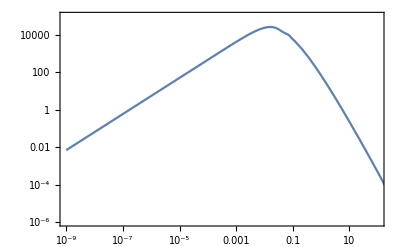

```mathematica
LogLogPlot[Plin[k],{k,10^-9,1000},Frame->True,PlotRange->{{0.000000001,100},{10^-6,10^5}}]
```

### Ξ0 Ξ2 by FFTLog

```mathematica
(* Nmax log k bins, from kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
Λresum =0.12;
CoeffPowIR[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Exp[-kn⟦i⟧^2/Λresum^2]/kn⟦i⟧^2 Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

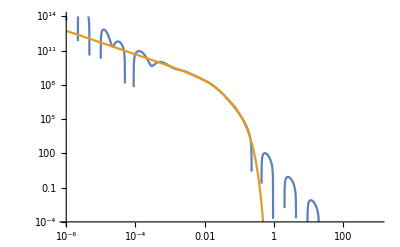

```mathematica
biasA=-2.6//N;
NmaxA=20;
kminA=10^-5;
kmaxA=20;
cnA=CoeffPowIR[biasA,NmaxA,kminA,kmaxA];
kn=kBins[NmaxA,kminA,kmaxA];
Pdq2[k_] = Re[ Total[cnA⟦All,1⟧k^cnA⟦All,2⟧]];
LogLogPlot[{Pdq2[k],Exp[-k^2/Λresum^2]/k^2 Plin[k]},{k,.000001,1000},PlotRange->{10^-4,10^14}]
```

```mathematica
Mtilde0=cnA⟦All,1⟧ * (-1/(2 π^2))Gamma[2 + cnA⟦All,2⟧] Sin[(cnA⟦All,2⟧ π)/2];
Mtilde2=cnA⟦All,1⟧ * (1/(2 π^2))√π 2^(1+cnA⟦All,2⟧)Gamma[(3+2+ cnA⟦All,2⟧)/2]/Gamma[(2-cnA⟦All,2⟧)/2] ;
Ξ0[q_] =Re[ Mtilde0.q^(-cnA⟦All,2⟧-3) ];
Ξ2[q_] =Re[ Mtilde2.q^(-cnA⟦All,2⟧-3) ];
Ξ0[q_] = -Ξ0[q]+Ξ0[0.01];
```

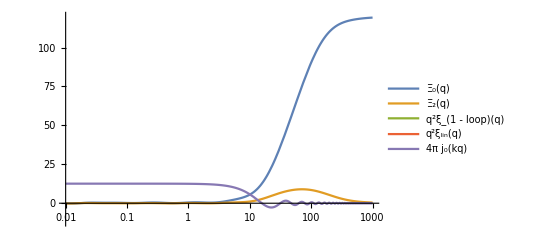

-Graphics-

```mathematica
ktest = 0.2 ;
p1=LogLinearPlot[{Ξ0[q] ,Ξ2[q],q^2 ξE1loopFFT[q],q^2 ξ11FFT[q] ,4π SphericalBesselJ[0,ktest q] }, { q , 10^-2, 1000},PlotRange->{-12,120},PlotLegends-> {"Ξ_0(q)", "Ξ_2(q)","q^2ξ_(1 - loop)(q)", "q^2ξ_lin(q)", "4π j_0(kq)" }]
(*Export["IRcorrections.pdf",p1]*)
```

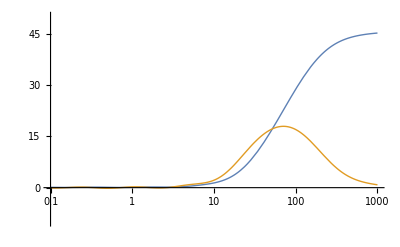

```mathematica
LogLinearPlot[{   2/3(Ξ0[q]-Ξ2[q]),2 Ξ2[q], X1[1][q] ,Y1[1][q]} , { q , 10^-1, 1000},PlotRange->{-10,50},PlotStyle->{Thick, Thick, Dashed ,Dashed}]
```

### IR-correction integrands

For fast computation, I compute only a, b, c up to 4 and l, lpr = 4 (which is enough at the order n_X and n_Y that we work)

```mathematica
SetDirectory[NotebookDirectory[]];
```

compute spherical bessel derivatives j_l^(c)(x)

```mathematica
Clear[jc]
Do[ Monitor[jc[c][l][x_] =  D[SphericalBesselJ[l,x],{x,c}]//Simplify ,{ c , l }], {c, 0,4} , {l , 0,8}]
```

compute n_j^b(l’)

```mathematica
Clear[n];
Do[ n[b][j][lpr] = Integrate[ (2(j + lpr) + 1)/2 μ^b LegendreP[j + lpr , μ ] LegendreP[lpr , μ] , { μ , -1 , 1}], { b, 0,4} , {j , -4,4} , {lpr,0,4,2}]
```

compute (I^a)_(l,l')(k,q)

```mathematica
orderTaylor = 5;
Do[ Monitor[Iint[a][l][lpr][k_,q_] = Integrate[(LegendreP[l,μk] μk^a Normal[ Series[ ⅇ^(-λ k^2/2(2+ff)ff X1 μk^2) , {λ , 0 , orderTaylor}]]LegendreP[lpr,μk]/.λ->1//FunctionExpand),{μk,-1,1}]//Simplify ,{a, l , lpr}], { a ,0,4}, {l,{0,2,4}} , {lpr,0,8}]
```

compute (L_(l,l'))^abc(k,q)

```mathematica
Clear[L];
Monitor[ Do[ L[a][b][c][l][lpr][k_,q_] = Sum[ ⅈ^c(-ⅈ)^j n[b][j][lpr] *jc[c][lpr + j][k q] *Iint[a][l][lpr+j][k,q] , {j , If[ lpr-b<0,-lpr,-b],b}] , {a,0,4},{b,0,4},{c,0,4},{l,0,4,2}, {lpr ,0,4,2}], { a, b,c,l,lpr}] ;
```

compute κ_abc(L_(l,l'))^abc(k,q) (||)_0

```mathematica
fullterm1 = Coefficient[ Series[ Exp[-1/2 λ k^2 Y1( kdq^2 + 2 ff μk μq kdq + ff^2 μk^2 μq^2)] , {λ , 0 , 1}]//Normal , λ^1]//Expand;
fullterm2 = Coefficient[ Series[ Exp[-1/2 λ k^2 Y1 ( kdq^2 + 2 ff μk μq kdq + ff^2 μk^2 μq^2)] , {λ , 0 , 2}]//Normal , λ^2]//Expand;
Clear[K1,K2]
K1[l_][lpr_][k_,q_] =  Sum[ Coefficient[ μk μq kdq fullterm1 , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];
K2[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq fullterm2 , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];
```

Q_0 for IR-resummation

```mathematica
Q0[k_,q_,l_,lpr_]=    (2l+1)/2 ⅇ^(-k^2/2 X1)   (L[0][0][0][l][lpr][k,q]+K1[l][lpr][k,q] +0K2[l][lpr][k,q] )  ;
```

Q_1 for IR-resummation

```mathematica
yorder =1;
exps = Exp[-1/2 λ1 k^2 Y1 ( kdq^2  + 2 ff μk μq kdq + ff^2 μk^2 μq^2)]Exp[ λ2 k^2/2( X1(1 + μk^2 ff(2+ff))  + Y1 ( kdq^2 + 2 μk μq ff kdq + ff^2 μk^2 μq^2))] ;
expand=(Series[ Series[ Series[ exps , { λ1 , 0 , yorder}]//Normal , {λ2, 0 ,1}]//Normal , { Y1 , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1} ;

J[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq expand , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}] ;
Q1[k_,q_,l_,lpr_]= (2l + 1)/2 ⅇ^(-k^2/2 X1) J[l][lpr][k,q] ;
```

```mathematica
foo=Replace[ToBoxes@#,InterpretationBox[a_,b_,c___]:>With[{aa=StringReplace[a,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow", "Pi"-> "M_PI","Cos"-> "cos","Sin"-> "sin"}]},aa],{0,Infinity}]&;
Q1tab = Table[foo@CForm[4π q^2 Q1[k,q,l,lpr]/.{ X1->X1q,Y1-> Y1q}] , { l , {0 ,2,4}} , {lpr,  0,4,2}] ;
OutputQ1= ExportString[ Q1tab,"Table","FieldSeparators"-> " | "];
Export["outputQ1.dat",OutputQ1];
Q0tab = Table[foo@CForm[4π q^2 Q0[k,q,l,lpr]/.{ X1->X1q,Y1-> Y1q}] , { l , {0 ,2,4}} , {lpr,  0,4,2}] ;
OutputQ = ExportString[ Q0tab,"Table","FieldSeparators"-> " | "];
Export["outputQ0.dat",OutputQ ];
```

```mathematica
SBrep5={SphericalBesselJ[5,x_]->9/x SphericalBesselJ[4,x]-SphericalBesselJ[3,x]};
SBrep3={SphericalBesselJ[3,x_]-> 5/x SphericalBesselJ[2,x]-SphericalBesselJ[1,x] };
SBrep1={SphericalBesselJ[1,x_]-> x/3(SphericalBesselJ[0,x]+SphericalBesselJ[2,x])};
Fakerep={SphericalBesselJ[0,x_ ]-> j0,SphericalBesselJ[2,x_ ]-> j2,  SphericalBesselJ[4,x_ ]-> j4,SphericalBesselJ[6,x_ ]-> j6};
ab={α-> 0,β-> 0};
```

```mathematica
Xp = {k^3 X1,k^5 X1^2,k^7 X1^3,k^9 X1^4,k^11 X1^5,k^13 X1^6,k^15 X1^7,k^17 X1^8};
YXp={k^3 Y1,k^5 Y1 X1,k^7 Y1 X1^2,k^9 Y1 X1^3,k^11 Y1 X1^4,k^13 Y1 X1^5,k^15 Y1 X1^6,k^17 Y1 X1^7};
jlist02 = {j0, j2};
jlist024={j0,j2};
jklist = {j0 k,j2 k,j4 k} ;
j2k2YXp={j2  k^3 X1 Y1,j2 k^5 X1^2 Y1,j2 k^7 X1^3 Y1,j2 k^9 X1^4 Y1, j2 k^11 X1^5 Y1,j2 k^13 X1^6 Y1,j2 k^15 X1^7 Y1,j2 k^17 X1^8 Y1};
j2k2YXpqm2={q^-2 j2  k^3 X1 Y1,q^-2 j2 k^5 X1^2 Y1,q^-2 j2 k^7 X1^3 Y1,q^-2 j2 k^9 X1^4 Y1, q^-2 j2 k^11 X1^5 Y1, q^-2 j2 k^13 X1^6 Y1, q^-2 j2 k^15 X1^7 Y1,q^-2 j2 k^17 X1^8 Y1};
megalist=Join[jklist,Outer[Times,Xp,  jlist02],Outer[Times,YXp,jlist024]]//Flatten
megalistq=Join[jklist,Outer[Times,Xp,  jlist02],Outer[Times,YXp,jlist024]]//Flatten
Length[megalistq]
```

{j0 k,j2 k,j4 k,j0 k^3 X1,j2 k^3 X1,j0 k^5 X1^2,j2 k^5 X1^2,j0 k^7 X1^3,j2 k^7 X1^3,j0 k^9 X1^4,j2 k^9 X1^4,j0 k^11 X1^5,j2 k^11 X1^5,j0 k^13 X1^6,j2 k^13 X1^6,j0 k^15 X1^7,j2 k^15 X1^7,j0 k^17 X1^8,j2 k^17 X1^8,j0 k^3 Y1,j2 k^3 Y1,j0 k^5 X1 Y1,j2 k^5 X1 Y1,j0 k^7 X1^2 Y1,j2 k^7 X1^2 Y1,j0 k^9 X1^3 Y1,j2 k^9 X1^3 Y1,j0 k^11 X1^4 Y1,j2 k^11 X1^4 Y1,j0 k^13 X1^5 Y1,j2 k^13 X1^5 Y1,j0 k^15 X1^6 Y1,j2 k^15 X1^6 Y1,j0 k^17 X1^7 Y1,j2 k^17 X1^7 Y1}

{j0 k,j2 k,j4 k,j0 k^3 X1,j2 k^3 X1,j0 k^5 X1^2,j2 k^5 X1^2,j0 k^7 X1^3,j2 k^7 X1^3,j0 k^9 X1^4,j2 k^9 X1^4,j0 k^11 X1^5,j2 k^11 X1^5,j0 k^13 X1^6,j2 k^13 X1^6,j0 k^15 X1^7,j2 k^15 X1^7,j0 k^17 X1^8,j2 k^17 X1^8,j0 k^3 Y1,j2 k^3 Y1,j0 k^5 X1 Y1,j2 k^5 X1 Y1,j0 k^7 X1^2 Y1,j2 k^7 X1^2 Y1,j0 k^9 X1^3 Y1,j2 k^9 X1^3 Y1,j0 k^11 X1^4 Y1,j2 k^11 X1^4 Y1,j0 k^13 X1^5 Y1,j2 k^13 X1^5 Y1,j0 k^15 X1^6 Y1,j2 k^15 X1^6 Y1,j0 k^17 X1^7 Y1,j2 k^17 X1^7 Y1}

35

```mathematica
coefQ1=Table[Coefficient[Series[k Q1[k, q, l,lp]/.SBrep3/.SBrep1/.Fakerep/.ab,{k,0,17}]//Normal,megalist]/.{X1-> 0,Y1-> 0,q-> 1}//Simplify,{l,{0,2}},{lp,{0,2}}] ;
coefQ1//MatrixForm
Table[(coefQ1⟦l/2+1,lp/2+1⟧.megalistq- Series[k Q1[k, q, l,lp]/.SBrep3/.SBrep1 /.Fakerep/.ab,{k,0,17}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]
```

((1
0
0
0
0
1/120 (-15-20 ff-22 ff^2-12 ff^3-3 ff^4)
0
1/840 (35+70 ff+119 ff^2+124 ff^3+81 ff^4+30 ff^5+5 ff^6)
0
(-315-840 ff-1932 ff^2-2952 ff^3-3098 ff^4-2200 ff^5-1020 ff^6-280 ff^7-35 ff^8)/40320
0
(693+2310 ff+6699 ff^2+13464 ff^3+19426 ff^4+20276 ff^5+15270 ff^6+8120 ff^7+2905 ff^8+630 ff^9+63 ff^10)/665280
0
(-15015-60060 ff-210210 ff^2-523380 ff^3-960245 ff^4-1320280 ff^5-1387404 ff^6-1121512 ff^7-685265 ff^8-303660 ff^9-91350 ff^10-16632 ff^11-1386 ff^12)/138378240
0
(6435+30030 ff+123123 ff^2+365508 ff^3+813527 ff^4+1386970 ff^5+1837335 ff^6+1848280 ff^7+1348025 ff^8+677250 ff^9+220185 ff^10+41580 ff^11+3465 ff^12)/691891200
0
(-6435-34320 ff-161304 ff^2-555984 ff^3-1454596 ff^4-2958800 ff^5-4633800 ff^6-5302160 ff^7-4211650 ff^8-2228400 ff^9-745560 ff^10-142560 ff^11-11880 ff^12)/9488793600
0
0
0
1/180 (-15-20 ff-22 ff^2-12 ff^3-3 ff^4)
1/630 (105+140 ff+133 ff^2+66 ff^3+12 ff^4)
1/840 (35+70 ff+119 ff^2+124 ff^3+81 ff^4+30 ff^5+5 ff^6)
(-105-210 ff-336 ff^2-336 ff^3-205 ff^4-70 ff^5-10 ff^6)/1260
(-315-840 ff-1932 ff^2-2952 ff^3-3098 ff^4-2200 ff^5-1020 ff^6-280 ff^7-35 ff^8)/30240
(3465+9240 ff+20559 ff^2+30690 ff^3+31207 ff^4+21380 ff^5+9465 ff^6+2450 ff^7+280 ff^8)/166320
(693+2310 ff+6699 ff^2+13464 ff^3+19426 ff^4+20276 ff^5+15270 ff^6+8120 ff^7+2905 ff^8+630 ff^9+63 ff^10)/399168
(-45045-150150 ff-426426 ff^2-844272 ff^3-1195766 ff^4-1222780 ff^5-899040 ff^6-464800 ff^7-160685 ff^8-33390 ff^9-3150 ff^10)/12972960
(-3003-12012 ff-42042 ff^2-104676 ff^3-192049 ff^4-264056 ff^5-274524 ff^6-215432 ff^7-125965 ff^8-53340 ff^9-15498 ff^10-2772 ff^11-231 ff^12)/13837824
(15015+60060 ff+207207 ff^2+510510 ff^3+925210 ff^4+1255280 ff^5+1285670 ff^6+992068 ff^7+568995 ff^8+235620 ff^9+66675 ff^10+11550 ff^11+924 ff^12)/34594560
(6435+30030 ff+123123 ff^2+365508 ff^3+813527 ff^4+1386970 ff^5+1837335 ff^6+1903192 ff^7+1540217 ff^8+965538 ff^9+460425 ff^10+161700 ff^11+39501 ff^12+6006 ff^13+429 ff^14)/296524800
(-765765-3573570 ff-14498484 ff^2-42707808 ff^3-94227991 ff^4-159148730 ff^5-208671090 ff^6-213722096 ff^7-170806867 ff^8-105586614 ff^9-49560000 ff^10-17094000 ff^11-4089393 ff^12-606606 ff^13-42042 ff^14)/17643225600
(-6435-34320 ff-161304 ff^2-555984 ff^3-1454596 ff^4-2958800 ff^5-4728840 ff^6-5916752 ff^7-5721202 ff^8-4195728 ff^9-2276100 ff^10-881100 ff^11-229581 ff^12-36036 ff^13-2574 ff^14)/3558297600
(109395+583440 ff+2720289 ff^2+9320454 ff^3+24224915 ff^4+48933820 ff^5+77603385 ff^6+96187258 ff^7+91894961 ff^8+66374712 ff^9+35346375 ff^10+13389750 ff^11+3404214 ff^12+519948 ff^13+36036 ff^14)/30245529600) | (0
0
0
0
0
0
-1/210 ff (14+19 ff+12 ff^2+3 ff^3)
0
(ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5))/1260
0
-(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/55440
0
(ff (6006+23595 ff+54912 ff^2+85748 ff^3+94060 ff^4+73170 ff^5+39760 ff^6+14420 ff^7+3150 ff^8+315 ff^9))/4324320
0
-(ff (30030+143715 ff+414700 ff^2+825175 ff^3+1194500 ff^4+1300454 ff^5+1078112 ff^6+670390 ff^7+300510 ff^8+91035 ff^9+16632 ff^10+1386 ff^11))/172972800
0
(ff (6006+33891 ff+116688 ff^2+282022 ff^3+506750 ff^4+695829 ff^5+716912 ff^6+530740 ff^7+269010 ff^8+87885 ff^9+16632 ff^10+1386 ff^11))/345945600
0
-(ff (858+5577 ff+22308 ff^2+63427 ff^3+136070 ff^4+220761 ff^5+258248 ff^6+207835 ff^7+110790 ff^8+37215 ff^9+7128 ff^10+594 ff^11))/593049600
0
0
(ff (70+123 ff+100 ff^2+28 ff^3))/4200
-(ff (294+357 ff+200 ff^2+44 ff^3))/2940
-(ff (70+239 ff+400 ff^2+349 ff^3+160 ff^4+30 ff^5))/12600
(ff (686+1414 ff+1580 ff^2+1017 ff^3+360 ff^4+55 ff^5))/8820
(ff (2310+15411 ff+42900 ff^2+65446 ff^3+60890 ff^4+34515 ff^5+11060 ff^6+1540 ff^7))/3326400
-(ff (61446+179025 ff+299640 ff^2+320318 ff^3+224650 ff^4+100665 ff^5+26320 ff^6+3080 ff^7))/2328480
-(ff^2 (12012+57200 ff+133757 ff^2+194470 ff^3+187375 ff^4+120820 ff^5+50435 ff^6+12390 ff^7+1365 ff^8))/21621600
(ff (168168+633633 ff+1412840 ff^2+2111122 ff^3+2213020 ff^4+1642840 ff^5+850640 ff^6+293510 ff^7+60900 ff^8+5775 ff^9))/30270240
(ff (-6006+7293 ff+128700 ff^2+466336 ff^3+974660 ff^4+1365294 ff^5+1346744 ff^6+945700 ff^7+465570 ff^8+153405 ff^9+30492 ff^10+2772 ff^11))/415134720
-(ff (1219218+5636631 ff+15701400 ff^2+30135040 ff^3+42038900 ff^4+43564362 ff^5+33692624 ff^6+19258540 ff^7+7922250 ff^8+2224215 ff^9+382536 ff^10+30492 ff^11))/1452971520
-(ff (-510510-1042899 ff+2917200 ff^2+22562111 ff^3+68062900 ff^4+130692600 ff^5+177848104 ff^6+178239110 ff^7+133005474 ff^8+73375365 ff^9+29170680 ff^10+7927227 ff^11+1321320 ff^12+102102 ff^13))/176432256000
(ff (12150138+66570504 ff+222436500 ff^2+521414803 ff^3+908117900 ff^4+1207852227 ff^5+1242589376 ff^6+991225270 ff^7+609077322 ff^8+283426710 ff^9+96769596 ff^10+22904343 ff^11+3363360 ff^12+231231 ff^13))/123502579200
(ff (-72930-269841 ff-243100 ff^2+1660594 ff^3+8554910 ff^4+22869505 ff^5+41588588 ff^6+53989120 ff^7+50143578 ff^8+32880105 ff^9+14817660 ff^10+4361544 ff^11+755040 ff^12+58344 ff^13))/201636864000
-(ff (1327326+8408829 ff+32769880 ff^2+90734202 ff^3+189468910 ff^4+305134139 ff^5+379405152 ff^6+360586940 ff^7+257761434 ff^8+135510795 ff^9+50651832 ff^10+12717936 ff^11+1921920 ff^12+132132 ff^13))/141145804800)
(0
0
0
0
0
-1/42 ff (14+19 ff+12 ff^2+3 ff^3)
0
1/252 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
0
-(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/11088
0
(ff (6006+23595 ff+54912 ff^2+85748 ff^3+94060 ff^4+73170 ff^5+39760 ff^6+14420 ff^7+3150 ff^8+315 ff^9))/864864
0
-(ff (30030+143715 ff+414700 ff^2+825175 ff^3+1194500 ff^4+1300454 ff^5+1078112 ff^6+670390 ff^7+300510 ff^8+91035 ff^9+16632 ff^10+1386 ff^11))/34594560
0
(ff (6006+33891 ff+116688 ff^2+282022 ff^3+506750 ff^4+695829 ff^5+716912 ff^6+530740 ff^7+269010 ff^8+87885 ff^9+16632 ff^10+1386 ff^11))/69189120
0
-(ff (858+5577 ff+22308 ff^2+63427 ff^3+136070 ff^4+220761 ff^5+258248 ff^6+207835 ff^7+110790 ff^8+37215 ff^9+7128 ff^10+594 ff^11))/118609920
0
0
0
-1/63 ff (14+19 ff+12 ff^2+3 ff^3)
1/126 ff (56+73 ff+42 ff^2+9 ff^3)
1/252 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
-(ff (924+2013 ff+2332 ff^2+1550 ff^3+560 ff^4+85 ff^5))/2772
-(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/8316
(ff (48048+146289 ff+253110 ff^2+279487 ff^3+201860 ff^4+92775 ff^5+24710 ff^6+2905 ff^7))/432432
(5 ff (6006+23595 ff+54912 ff^2+85748 ff^3+94060 ff^4+73170 ff^5+39760 ff^6+14420 ff^7+3150 ff^8+315 ff^9))/2594592
-(ff (60060+234663 ff+538824 ff^2+828932 ff^3+893680 ff^4+681498 ff^5+361816 ff^6+127652 ff^7+26964 ff^8+2583 ff^9))/2594592
-(ff (6006+28743 ff+82940 ff^2+165035 ff^3+238900 ff^4+257134 ff^5+206752 ff^6+122990 ff^7+52710 ff^8+15435 ff^9+2772 ff^10+231 ff^11))/3459456
(ff (408408+1947231 ff+5566990 ff^2+10964915 ff^3+15691000 ff^4+16673022 ff^5+13213844 ff^6+7732830 ff^7+3252480 ff^8+931875 ff^9+163086 ff^10+13167 ff^11))/117621504
(ff (102102+576147 ff+1983696 ff^2+4794374 ff^3+8614750 ff^4+11829093 ff^5+12571888 ff^6+10367924 ff^7+6591186 ff^8+3175725 ff^9+1123584 ff^10+275814 ff^11+42042 ff^12+3003 ff^13))/504092160
-(ff (27159132+152839401 ff+522674724 ff^2+1253913778 ff^3+2234643200 ff^4+3040883823 ff^5+3199917224 ff^6+2610171676 ff^7+1639270332 ff^8+779126775 ff^9+271444404 ff^10+65470482 ff^11+9777768 ff^12+681681 ff^13))/67044257280
-(ff (58344+379236 ff+1516944 ff^2+4313036 ff^3+9252760 ff^4+15334884 ff^5+19683424 ff^6+19380572 ff^7+14395608 ff^8+7878600 ff^9+3067812 ff^10+802197 ff^11+126126 ff^12+9009 ff^13))/3024552960
(ff (31039008+201337851 ff+801194394 ff^2+2265171545 ff^3+4829541220 ff^4+7949275803 ff^5+10119278134 ff^6+9860017601 ff^7+7228939032 ff^8+3894693705 ff^9+1489227894 ff^10+381565107 ff^11+58666608 ff^12+4090086 ff^13))/804531087360) | (0
1
0
0
0
0
1/168 (-21-44 ff-58 ff^2-36 ff^3-9 ff^4)
0
(231+726 ff+1551 ff^2+1868 ff^3+1317 ff^4+510 ff^5+85 ff^6)/5544
0
(-9009-37752 ff-111540 ff^2-198744 ff^3-228766 ff^4-172520 ff^5-82980 ff^6-23240 ff^7-2905 ff^8)/1153152
0
(9009+47190 ff+178035 ff^2+419640 ff^3+668810 ff^4+746356 ff^5+588390 ff^6+322840 ff^7+117845 ff^8+25830 ff^9+2583 ff^10)/8648640
0
(-255255-1604460 ff-7365930 ff^2-21591700 ff^3-43936925 ff^4-64830520 ff^5-71694428 ff^6-60174184 ff^7-37759505 ff^8-17031420 ff^9-5179230 ff^10-948024 ff^11-79002 ff^12)/2352430080
0
(21879+160446 ff+867867 ff^2+3041844 ff^3+7529011 ff^4+13807706 ff^5+19274679 ff^6+20098232 ff^7+14996485 ff^8+7637490 ff^9+2501793 ff^10+474012 ff^11+39501 ff^12)/2352430080
0
(-153153-1283568 ff-7993128 ff^2-32598384 ff^3-95019596 ff^4-208246192 ff^5-343517496 ff^6-406397488 ff^7-329343350 ff^8-176274000 ff^9-59340456 ff^10-11376288 ff^11-948024 ff^12)/225833287680
0
0
(-35+2 ff+91 ff^2+100 ff^3+32 ff^4)/1680
(-245-462 ff-545 ff^2-300 ff^3-66 ff^4)/1176
(1155+1144 ff-2794 ff^2-8380 ff^3-8897 ff^4-4460 ff^5-880 ff^6)/110880
(8085+23716 ff+47168 ff^2+52700 ff^3+34341 ff^4+12240 ff^5+1870 ff^6)/77616
(-45045-91806 ff+23595 ff^2+461760 ff^3+952577 ff^4+1006450 ff^5+611385 ff^6+203980 ff^7+29120 ff^8)/17297280
(-315315-1255254 ff-3518229 ff^2-5935800 ff^3-6456811 ff^4-4591670 ff^5-2077815 ff^6-546140 ff^7-63910 ff^8)/12108096
(15015+46332 ff+46332 ff^2-133640 ff^3-553582 ff^4-966800 ff^5-1020100 ff^6-693560 ff^7-299425 ff^8-75180 ff^9-8400 ff^10)/34594560
(105105+528528 ff+1912482 ff^2+4318600 ff^3+6586006 ff^4+7023496 ff^5+5283944 ff^6+2762648 ff^7+959441 ff^8+199752 ff^9+18942 ff^10)/24216192
(-765765-3165162 ff-6439719 ff^2+198900 ff^3+34711790 ff^4+97981540 ff^5+155370642 ff^6+163957024 ff^7+120056615 ff^8+60772950 ff^9+20411685 ff^10+4110876 ff^11+376992 ff^12)/14114580480
(-5360355-32570538 ff-144452451 ff^2-408739500 ff^3-802234420 ff^4-1140739100 ff^5-1200311862 ff^6-939355424 ff^7-541754395 ff^8-224309610 ff^9-63248535 ff^10-10902276 ff^11-869022 ff^12)/9880206336
(14549535+75380448 ff+224755674 ff^2+270835500 ff^3-463159067 ff^4-2776385260 ff^5-6428200308 ff^6-9561820744 ff^7-10093994855 ff^8-7790921208 ff^9-4399379670 ff^10-1778322084 ff^11-489097917 ff^12-82222140 ff^13-6390384 ff^14)/2681770291200
(101846745+725536812 ff+3810592500 ff^2+12961053300 ff^3+31113839671 ff^4+55307122040 ff^5+74783927838 ff^6+77946126440 ff^7+62820985255 ff^8+38912019804 ff^9+18218238360 ff^10+6248042724 ff^11+1483245225 ff^12+218137920 ff^13+14996982 ff^14)/1877239203840
(-4849845-30207606 ff-117366249 ff^2-245725480 ff^3-113857177 ff^4+977000710 ff^5+3720819571 ff^6+7698694108 ff^7+10669867985 ff^8+10294074966 ff^9+6913913265 ff^10+3166110948 ff^11+942381594 ff^12+164444280 ff^13+12780768 ff^14)/10727081164800
(-33948915-277411134 ff-1683727617 ff^2-6689846800 ff^3-18989300169 ff^4-40508641250 ff^5-66363948581 ff^6-83618177580 ff^7-80270077195 ff^8-57805024578 ff^9-30550231215 ff^10-11460369228 ff^11-2883933360 ff^12-436275840 ff^13-29993964 ff^14)/7508956815360))

```mathematica
Export["../cbirdy/Q100.txt",Table[FortranForm[coefQ1⟦1,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
Export["../cbirdy/Q102.txt",Table[FortranForm[coefQ1⟦1,2,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
Export["../cbirdy/Q120.txt",Table[FortranForm[coefQ1⟦2,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
Export["../cbirdy/Q122.txt",Table[FortranForm[coefQ1⟦2,2,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
```

```mathematica
coefQ0=Table[Coefficient[Series[k Q0[k, q, l,lp]/.SBrep3/.SBrep1/.Fakerep/.ab,{k,0,17}]//Normal,megalist]/.{X1-> 0,Y1-> 0}/.{q-> 1}//Simplify,{l,{0,2}},{lp,{0,2}}] ;
Table[(coefQ0⟦l/2+1,lp/2+1⟧.megalistq- Series[k Q0[k, q, l,lp]/.SBrep3/.SBrep1 /.Fakerep/.ab,{k,0,15}]//Normal)//Simplify,{l,{0,2}},{lp,{0,2}}]
coefQ0//MatrixForm
```

((1
0
0
1/6 (-3-2 ff-ff^2)
0
1/120 (15+20 ff+22 ff^2+12 ff^3+3 ff^4)
0
(-35-70 ff-119 ff^2-124 ff^3-81 ff^4-30 ff^5-5 ff^6)/1680
0
1/48 (1/8+1/6 ff (2+ff)+3/20 ff^2 (2+ff)^2+1/14 ff^3 (2+ff)^3+1/72 ff^4 (2+ff)^4)
0
1/240 (-1/16-5/48 ff (2+ff)-1/8 ff^2 (2+ff)^2-5/56 ff^3 (2+ff)^3-5/144 ff^4 (2+ff)^4-1/176 ff^5 (2+ff)^5)
0
(1/32+1/16 ff (2+ff)+3/32 ff^2 (2+ff)^2+5/56 ff^3 (2+ff)^3+5/96 ff^4 (2+ff)^4+3/176 ff^5 (2+ff)^5)/1440
0
(-495-1155 ff (2+ff)-2079 ff^2 (2+ff)^2-2475 ff^3 (2+ff)^3-1925 ff^4 (2+ff)^4-945 ff^5 (2+ff)^5)/319334400
0
(1/128+1/48 ff (2+ff)+7/160 ff^2 (2+ff)^2+1/16 ff^3 (2+ff)^3+35/576 ff^4 (2+ff)^4+7/176 ff^5 (2+ff)^5)/80640
0
1/18 (-3-2 ff-ff^2)
1/45 (15+10 ff+2 ff^2)
1/180 (15+20 ff+22 ff^2+12 ff^3+3 ff^4)
1/630 (-105-140 ff-133 ff^2-66 ff^3-12 ff^4)
(-35-70 ff-119 ff^2-124 ff^3-81 ff^4-30 ff^5-5 ff^6)/1680
(105+210 ff+336 ff^2+336 ff^3+205 ff^4+70 ff^5+10 ff^6)/2520
(315+840 ff+1932 ff^2+2952 ff^3+3098 ff^4+2200 ff^5+1020 ff^6+280 ff^7+35 ff^8)/90720
(-3465-9240 ff-20559 ff^2-30690 ff^3-31207 ff^4-21380 ff^5-9465 ff^6-2450 ff^7-280 ff^8)/498960
(-693-2310 ff-6699 ff^2-13464 ff^3-19426 ff^4-20276 ff^5-15270 ff^6-8120 ff^7-2905 ff^8-630 ff^9-63 ff^10)/1596672
(45045+150150 ff+426426 ff^2+844272 ff^3+1195766 ff^4+1222780 ff^5+899040 ff^6+464800 ff^7+160685 ff^8+33390 ff^9+3150 ff^10)/51891840
(3003+12012 ff+42042 ff^2+104676 ff^3+192049 ff^4+264056 ff^5+274524 ff^6+215432 ff^7+125965 ff^8+53340 ff^9+15498 ff^10+2772 ff^11+231 ff^12)/69189120
(-15015-60060 ff-207207 ff^2-510510 ff^3-925210 ff^4-1255280 ff^5-1285670 ff^6-992068 ff^7-568995 ff^8-235620 ff^9-66675 ff^10-11550 ff^11-924 ff^12)/172972800
(-6435-30030 ff-123123 ff^2-365508 ff^3-813527 ff^4-1386970 ff^5-1805655 ff^6-1753240 ff^7-1229225 ff^8-598050 ff^9-190485 ff^10-35640 ff^11-2970 ff^12)/1779148800
(45045+210210 ff+852852 ff^2+2512224 ff^3+5542823 ff^4+9361690 ff^5+12053010 ff^6+11522224 ff^7+7904435 ff^8+3740310 ff^9+1152900 ff^10+207900 ff^11+16632 ff^12)/6227020800
(6435+34320 ff+161304 ff^2+555984 ff^3+1454596 ff^4+2958800 ff^5+4538760 ff^6+5017040 ff^7+3855250 ff^8+1990800 ff^9+656460 ff^10+124740 ff^11+10395 ff^12)/24908083200
(-6435-34320 ff-160017 ff^2-548262 ff^3-1424995 ff^4-2878460 ff^5-4374825 ff^6-4758362 ff^7-3568705 ff^8-1786680 ff^9-568575 ff^10-103950 ff^11-8316 ff^12)/12454041600) | (0
0
0
0
-1/15 ff (2+ff)
0
1/210 ff (14+19 ff+12 ff^2+3 ff^3)
0
-(ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5))/2520
0
(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/166320
0
-(ff (6006+23595 ff+54912 ff^2+85748 ff^3+94060 ff^4+73170 ff^5+39760 ff^6+14420 ff^7+3150 ff^8+315 ff^9))/17297280
0
(ff (6006+28743 ff+82940 ff^2+165035 ff^3+238900 ff^4+242350 ff^5+162400 ff^6+67550 ff^7+15750 ff^8+1575 ff^9))/172972800
0
-(ff (6006+33891 ff+116688 ff^2+282022 ff^3+506750 ff^4+607125 ff^5+450800 ff^6+198100 ff^7+47250 ff^8+4725 ff^9))/2075673600
0
(ff (858+5577 ff+22308 ff^2+63427 ff^3+136070 ff^4+182745 ff^5+144200 ff^6+65275 ff^7+15750 ff^8+1575 ff^9))/4151347200
1/45 ff (2+ff)
-1/315 ff (28+11 ff)
-(ff (70+123 ff+100 ff^2+28 ff^3))/4200
(ff (294+357 ff+200 ff^2+44 ff^3))/2940
(ff (70+239 ff+400 ff^2+349 ff^3+160 ff^4+30 ff^5))/25200
-(ff (686+1414 ff+1580 ff^2+1017 ff^3+360 ff^4+55 ff^5))/17640
-(ff (2310+15411 ff+42900 ff^2+65446 ff^3+60890 ff^4+34515 ff^5+11060 ff^6+1540 ff^7))/9979200
(ff (61446+179025 ff+299640 ff^2+320318 ff^3+224650 ff^4+100665 ff^5+26320 ff^6+3080 ff^7))/6985440
(ff^2 (12012+57200 ff+133757 ff^2+194470 ff^3+187375 ff^4+120820 ff^5+50435 ff^6+12390 ff^7+1365 ff^8))/86486400
-(ff (168168+633633 ff+1412840 ff^2+2111122 ff^3+2213020 ff^4+1642840 ff^5+850640 ff^6+293510 ff^7+60900 ff^8+5775 ff^9))/121080960
-(ff (-6006+7293 ff+128700 ff^2+466336 ff^3+974660 ff^4+1365294 ff^5+1346744 ff^6+945700 ff^7+465570 ff^8+153405 ff^9+30492 ff^10+2772 ff^11))/2075673600
(ff (1219218+5636631 ff+15701400 ff^2+30135040 ff^3+42038900 ff^4+43564362 ff^5+33692624 ff^6+19258540 ff^7+7922250 ff^8+2224215 ff^9+382536 ff^10+30492 ff^11))/7264857600
(ff (-30030-61347 ff+171600 ff^2+1327183 ff^3+4003700 ff^4+7909560 ff^5+10765160 ff^6+9846550 ff^7+5868450 ff^8+2178225 ff^9+457380 ff^10+41580 ff^11))/62270208000
-(ff (714714+3915912 ff+13084500 ff^2+30671459 ff^3+53418700 ff^4+69497811 ff^5+66220672 ff^6+44968070 ff^7+21026250 ff^8+6412770 ff^9+1147608 ff^10+91476 ff^11))/43589145600
-(ff (-4290-15873 ff-14300 ff^2+97682 ff^3+503230 ff^4+1471985 ff^5+2619820 ff^6+2811200 ff^7+1832250 ff^8+712425 ff^9+152460 ff^10+13860 ff^11))/83026944000
(ff (78078+494637 ff+1927640 ff^2+5337306 ff^3+11145230 ff^4+17062027 ff^5+18390624 ff^6+13588540 ff^7+6704250 ff^8+2108715 ff^9+382536 ff^10+30492 ff^11))/58118860800)
(0
0
0
-1/3 ff (2+ff)
0
1/42 ff (14+19 ff+12 ff^2+3 ff^3)
0
-1/504 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
0
(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/33264
0
-(ff (6006+23595 ff+54912 ff^2+85748 ff^3+94060 ff^4+73170 ff^5+39760 ff^6+14420 ff^7+3150 ff^8+315 ff^9))/3459456
0
(ff (6006+28743 ff+82940 ff^2+165035 ff^3+238900 ff^4+242350 ff^5+162400 ff^6+67550 ff^7+15750 ff^8+1575 ff^9))/34594560
0
-(ff (6006+33891 ff+116688 ff^2+282022 ff^3+506750 ff^4+607125 ff^5+450800 ff^6+198100 ff^7+47250 ff^8+4725 ff^9))/415134720
0
(ff (858+5577 ff+22308 ff^2+63427 ff^3+136070 ff^4+182745 ff^5+144200 ff^6+65275 ff^7+15750 ff^8+1575 ff^9))/830269440
0
-1/9 ff (2+ff)
1/63 ff (28+11 ff)
1/63 ff (14+19 ff+12 ff^2+3 ff^3)
-1/126 ff (56+73 ff+42 ff^2+9 ff^3)
-1/504 ff (42+93 ff+112 ff^2+78 ff^3+30 ff^4+5 ff^5)
(ff (924+2013 ff+2332 ff^2+1550 ff^3+560 ff^4+85 ff^5))/5544
(ff (462+1419 ff+2508 ff^2+2837 ff^3+2110 ff^4+1005 ff^5+280 ff^6+35 ff^7))/24948
-(ff (48048+146289 ff+253110 ff^2+279487 ff^3+201860 ff^4+92775 ff^5+24710 ff^6+2905 ff^7))/1297296
-(5 ff (6006+23595 ff+54912 ff^2+85748 ff^3+94060 ff^4+73170 ff^5+39760 ff^6+14420 ff^7+3150 ff^8+315 ff^9))/10378368
(ff (60060+234663 ff+538824 ff^2+828932 ff^3+893680 ff^4+681498 ff^5+361816 ff^6+127652 ff^7+26964 ff^8+2583 ff^9))/10378368
(ff (6006+28743 ff+82940 ff^2+165035 ff^3+238900 ff^4+257134 ff^5+206752 ff^6+122990 ff^7+52710 ff^8+15435 ff^9+2772 ff^10+231 ff^11))/17297280
-(ff (408408+1947231 ff+5566990 ff^2+10964915 ff^3+15691000 ff^4+16673022 ff^5+13213844 ff^6+7732830 ff^7+3252480 ff^8+931875 ff^9+163086 ff^10+13167 ff^11))/588107520
-(ff (6006+33891 ff+116688 ff^2+282022 ff^3+506750 ff^4+683157 ff^5+678896 ff^6+483220 ff^7+237330 ff^8+76005 ff^9+14256 ff^10+1188 ff^11))/177914880
(ff (1429428+8044179 ff+27509196 ff^2+65995462 ff^3+117612800 ff^4+157030581 ff^5+153987512 ff^6+107627380 ff^7+51668820 ff^8+16115085 ff^9+2935548 ff^10+237006 ff^11))/21171870720
(ff (3432+22308 ff+89232 ff^2+253708 ff^3+544280 ff^4+864036 ff^5+975968 ff^6+760060 ff^7+395640 ff^8+131040 ff^9+24948 ff^10+2079 ff^11))/1245404160
-(ff (1633632+10596729 ff+42168126 ff^2+119219555 ff^3+254186380 ff^4+400287321 ff^5+446018482 ff^6+340447835 ff^7+172819080 ff^8+55634355 ff^9+10274418 ff^10+829521 ff^11))/296406190080) | (0
1
0
0
1/42 (-21-22 ff-11 ff^2)
0
1/168 (21+44 ff+58 ff^2+36 ff^3+9 ff^4)
0
(-231-726 ff-1551 ff^2-1868 ff^3-1317 ff^4-510 ff^5-85 ff^6)/11088
0
(9009+37752 ff+111540 ff^2+198744 ff^3+228766 ff^4+172520 ff^5+82980 ff^6+23240 ff^7+2905 ff^8)/3459456
0
(-9009-47190 ff-178035 ff^2-419640 ff^3-668810 ff^4-746356 ff^5-588390 ff^6-322840 ff^7-117845 ff^8-25830 ff^9-2583 ff^10)/34594560
0
(3003+18876 ff+86658 ff^2+254020 ff^3+516905 ff^4+762712 ff^5+783980 ff^6+529480 ff^7+221165 ff^8+51660 ff^9+5166 ff^10)/138378240
0
(-1287-9438 ff-51051 ff^2-178932 ff^3-442883 ff^4-812218 ff^5-985095 ff^6-736120 ff^7-324485 ff^8-77490 ff^9-7749 ff^10)/830269440
0
(9009+75504 ff+470184 ff^2+1917552 ff^3+5589388 ff^4+12249776 ff^5+16637880 ff^6+13198640 ff^7+5989270 ff^8+1446480 ff^9+144648 ff^10)/92990177280
-1/24+(29 ff)/630+(2 ff^2)/45
(-735-616 ff-242 ff^2)/1764
(35-2 ff-91 ff^2-100 ff^3-32 ff^4)/1680
(245+462 ff+545 ff^2+300 ff^3+66 ff^4)/1176
(-1155-1144 ff+2794 ff^2+8380 ff^3+8897 ff^4+4460 ff^5+880 ff^6)/221760
(-8085-23716 ff-47168 ff^2-52700 ff^3-34341 ff^4-12240 ff^5-1870 ff^6)/155232
(45045+91806 ff-23595 ff^2-461760 ff^3-952577 ff^4-1006450 ff^5-611385 ff^6-203980 ff^7-29120 ff^8)/51891840
(315315+1255254 ff+3518229 ff^2+5935800 ff^3+6456811 ff^4+4591670 ff^5+2077815 ff^6+546140 ff^7+63910 ff^8)/36324288
(-15015-46332 ff-46332 ff^2+133640 ff^3+553582 ff^4+966800 ff^5+1020100 ff^6+693560 ff^7+299425 ff^8+75180 ff^9+8400 ff^10)/138378240
(-105105-528528 ff-1912482 ff^2-4318600 ff^3-6586006 ff^4-7023496 ff^5-5283944 ff^6-2762648 ff^7-959441 ff^8-199752 ff^9-18942 ff^10)/96864768
(765765+3165162 ff+6439719 ff^2-198900 ff^3-34711790 ff^4-97981540 ff^5-155370642 ff^6-163957024 ff^7-120056615 ff^8-60772950 ff^9-20411685 ff^10-4110876 ff^11-376992 ff^12)/70572902400
(5360355+32570538 ff+144452451 ff^2+408739500 ff^3+802234420 ff^4+1140739100 ff^5+1200311862 ff^6+939355424 ff^7+541754395 ff^8+224309610 ff^9+63248535 ff^10+10902276 ff^11+869022 ff^12)/49401031680
(-765765-3967392 ff-11829246 ff^2-14254500 ff^3+24376793 ff^4+146125540 ff^5+350966652 ff^6+522521944 ff^7+501180365 ff^8+307125000 ff^9+116044110 ff^10+24665256 ff^11+2261952 ff^12)/846874828800
(-5360355-38186148 ff-200557500 ff^2-682160700 ff^3-1637570509 ff^4-2910901160 ff^5-3847513962 ff^6-3708394424 ff^7-2538283405 ff^8-1193047380 ff^9-365000580 ff^10-65413656 ff^11-5214132 ff^12)/592812380160
(255255+1589874 ff+6177171 ff^2+12932920 ff^3+5992483 ff^4-51421090 ff^5-221113249 ff^6-443730868 ff^7-501406955 ff^8-335946450 ff^9-132885795 ff^10-28776132 ff^11-2638944 ff^12)/3952082534400
(1786785+14600586 ff+88617243 ff^2+352097200 ff^3+999436851 ff^4+2132033750 ff^5+3315874919 ff^6+3612890148 ff^7+2688572425 ff^8+1332462390 ff^9+420198765 ff^10+76315932 ff^11+6083154 ff^12)/2766457774080))

```mathematica
Export["../cbirdy/Q000.txt",Table[FortranForm[coefQ0⟦1,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
Export["../cbirdy/Q002.txt",Table[FortranForm[coefQ0⟦1,2,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
Export["../cbirdy/Q020.txt",Table[FortranForm[coefQ0⟦2,1,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
Export["../cbirdy/Q022.txt",Table[FortranForm[coefQ0⟦2,2,i⟧],{i,4,Length[coefQ1⟦1,1⟧]}], "Table"];
```